# Basic functions and settings

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
compileOptionsPar={Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
densityPlotOptionsWithoutLegend={PlotRange->Full,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
plotOptions={Frame->True,PerformanceGoal->"Quality",Evaluate@font,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Axes->False};
```

```mathematica
density1={Evaluate@font,ColorFunction->"SunsetColors"};
density2={PerformanceGoal->"Quality",FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors",PlotLegends->True,ImageSize->310};
density3={PerformanceGoal->"Quality",FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors",PlotLegends->True,ImageSize->410};
export1={"AllowRasterization"->True,ImageResolution->800};
plot1={Frame->True,Evaluate@font,Axes->False};
plot2={Frame->True,PerformanceGoal->"Quality",ImageSize->310,Evaluate@font,Axes->False,PlotStyle->Thickness[0.004]};
```

```mathematica
cross=Graphics[{Line[{{-1,-1},{1,1}}],Line[{{1,-1},{-1,1}}]}];
```

# Defining first order perturbation Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

```mathematica
nn=5;
```

```mathematica
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(-5/2-λ/4 | -χ/(2 √5) | -λ/(√10) | 0 | 0 | 0
-χ/(2 √5) | 1/20 (-30-13 λ-4 χ^2) | -(3 √2 χ)/5 | -(3 λ)/(5 √2) | 0 | 0
-λ/(√10) | -(3 √2 χ)/5 | 1/20 (-17 λ-2 (5+8 χ^2)) | -(3 χ)/2 | -(3 λ)/(5 √2) | 0
0 | -(3 λ)/(5 √2) | -(3 χ)/2 | 1/20 (10-17 λ-36 χ^2) | -(7 √2 χ)/5 | -λ/(√10)
0 | 0 | -(3 λ)/(5 √2) | -(7 √2 χ)/5 | 1/20 (30-13 λ-64 χ^2) | -(9 χ)/(2 √5)
0 | 0 | 0 | -λ/(√10) | -(9 χ)/(2 √5) | 5/2-λ/4-5 χ^2)

### Metric tensor

```mathematica
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]:=Module[{g11,g12,g22,energies,eigenvectors},
energies=Eigenvalues[H[λ,χ]];
eigenvectors=Map[Normalize,Eigenvectors[H[λ,χ]]];
g11=Re@Sum[((Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH1[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]]Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]])/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenvectors[[1]]].DH2[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
gk[λ_,χ_,k_]:=Module[{g11,g12,g22,energies,eigenvectors,sumInd},
energies=Eigenvalues[H[λ,χ]];
eigenvectors=Map[Normalize,Eigenvectors[H[λ,χ]]];
sumInd=Delete[Table[m,{m,1 ,dim}],k];
g11=Re@Sum[((Conjugate[eigenvectors[[k]]].DH1[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH1[λ,χ].eigenvectors[[k]]))/(energies[[k]]-energies[[i]])^2,{i,sumInd}];
g12=Re@Sum[(Conjugate[eigenvectors[[k]]].DH1[λ,χ].eigenvectors[[i]]Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[k]])/(energies[[k]]-energies[[i]])^2,{i,sumInd}];
g22=Re@Sum[((Conjugate[eigenvectors[[k]]].DH2[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[k]]))/(energies[[k]]-energies[[i]])^2,{i,sumInd}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
DHC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@{D[H[λ,χ],λ],D[H[λ,χ],χ]},Evaluate@compileOptions];
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];

M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
gkC[λ_?NumericQ,χ_?NumericQ,k_?NumericQ]:=Module[{enNonSort,en,eigNonSort,sumInd,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
sumInd=Delete[Table[m,{m,1 ,dim}],k];
M1=Conjugate[eig⟦k⟧].DH1C[λ,χ].eig⟦#⟧&/@sumInd;
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦k⟧&/@sumInd;

M2=Conjugate[eig⟦k⟧].DH2C[λ,χ].eig⟦#⟧&/@sumInd;
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦k⟧&/@sumInd;
endif=(en⟦k⟧-en⟦#⟧)^2&/@sumInd;
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
EigensystemSorted[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
{en,eig}
]
GroundState[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
eig[[1]]
]
```

### General metric tensor and symplectic form

```mathematica
(*DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
psi[aList_]:=aList;
G[λ_,χ_,psi_,{L1_,L2_}]:=Module[{h,g11,g12,g22,energies,eigenvectors},
h=H[λ,χ];
energies=Eigenvalues[h];
eigenvectors=Map[Normalize,Eigenvectors[h]];
g11=Re[-Conjugate[h.psi L1].h.psi L1+Conjugate[h.psi L1].psi Conjugate[psi].h.psi L1 ];
g12=Re[-Conjugate[h.psi L1].h.psi L2+Conjugate[h.psi L1].psi Conjugate[psi].h.psi L2 ];
g22=Re[-Conjugate[h.psi L2].h.psi L2+Conjugate[h.psi L2].psi Conjugate[psi].h.psi L2 ];
{{g11,g12},{g12,g22}}
]
Ω[λ_,χ_,psi_,{L1_,L2_}]:=Module[{h,g11,g12,g22,energies,eigenvectors},
h=H[λ,χ];
energies=Eigenvalues[h];
eigenvectors=Map[Normalize,Eigenvectors[h]];
g11=Conjugate[h.psi L1].psi Conjugate[psi].h.psi L1 ;
g12=Conjugate[h.psi L1].psi Conjugate[psi].h.psi L2 ;
g22=Conjugate[h.psi L2].psi Conjugate[psi].h.psi L2 ;
{{g11,g12},{g12,g22}}
]*)
```

### Define area for derivative precision

Using observed formula for left and right singularity, see chapter Degeneracy of E0 and E1.

```mathematica
sR[n_]:={1/(1-n),√(n/(2n-1))}
sL[n_]:=If[OddQ[n],{1-n/2,√(n/(n+2))},{1-n,√(n/(n+1))}]
```

```mathematica
{r1,r2}=sR[nn];
{l1,l2}=sL[nn];
derPiece[λ_?NumericQ,χ_?NumericQ]:=Piecewise[{{14,λ>1&&-0.4<χ<0.4}},Round[3+10/(0.8+(λ-r1)^2+(Abs[χ]-r2)^2)]+Round[3+10/(0.8+(λ-l1)^2+(Abs[χ]-l2)^2)]];
derPieceC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@derPiece[λ,χ],Evaluate@compileOptions];
Plot3D[derPiece[λ,χ],{λ,-10,10},{χ,-5,5},PlotLegends->Automatic,PlotPoints->20,PlotRange->All,ColorFunction->"SunsetColors"]
```

-Graphics3D-

### Christoffel Symbols

G1[i,j]=(Γ^1)_ij,G2[i,j]=(Γ^2)_ij

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

### Ricci scalar and tensor

#### Basic Ricci formula

```mathematica
RicciScalar[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,g1,g2},
derTerms=derPiece[λ,χ];
g1=G1[λ,χ];
g2=G2[λ,χ];
2/(gC[λ,χ]⟦1,1⟧)(ND[G2[λ,c],c,χ,Terms->derTerms]⟦1⟧-ND[G2[l,χ],l,λ,Terms->derTerms]⟦2⟧+g2⟦3⟧g2⟦1⟧+g2⟦2⟧g1⟦1⟧-g2⟦2⟧g2⟦2⟧-g2⟦1⟧g1⟦2⟧)
]
```

#### Faster Ricci formula

```mathematica
R1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,g,l,c,dg1,dg2,R12},
derTerms=derPiece[λ,χ];
g=gC[λ,χ];
dg1=ND[gC[l,χ],l,λ,Terms->derTerms];
dg2=ND[gC[λ,c],c,χ,Terms->derTerms];
1/(√Det[g])(g⟦1,2⟧/g⟦1,1⟧dg2⟦1,1⟧-dg1⟦2,2⟧)
]
R2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,g,l,c,dg1,dg2,R12},
derTerms=derPiece[λ,χ];
g=gC[λ,χ];
dg1=ND[gC[l,χ],l,λ,Terms->derTerms];
dg2=ND[gC[λ,c],c,χ,Terms->derTerms];
1/(√Det[g])(2dg1⟦1,2⟧-dg2⟦1,1⟧-g⟦1,2⟧/g⟦1,1⟧dg1⟦1,1⟧)
]
Ric[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,l,c,g},
derTerms=derPiece[λ,χ];
g=gC[λ,χ];
1/(√Det[g])(ND[R1[l,χ],l,λ,Terms->derTerms]+ND[R2[λ,c],c,χ,Terms->derTerms])]
```

```mathematica
eigensys[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First]
]
eigensys1[λ_?NumericQ,χ_?NumericQ]:=
Sort@Eigenvalues[HC[λ,χ],Method->{"Banded"}
]
```

# Printing functions

### Print Hamiltonian

```mathematica
PrintHamiltonian[nn_]:=Module[{jj,dim,f,HH,H},
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ,χ]//FullSimplify
]
```

```mathematica
PrintHamiltonianV[nn_,{l_,x_}]:=Module[{jj,dim,f,HH,H},
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]/.{λ->l,χ->x}
]
```

### Print Determinant

```mathematica
PrintDeterminant[nn_,λmin_,λmax_,χmin_,χmax_,pp_,switch_,sw_]:=Module[{jj,dim,f,HH,H,HC,DH1C,DH2C,gC},
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];

DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];

M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
];
Which[switch==0&&sw==0, DensityPlot[Det[gC[λ,χ]],{λ,λmin,λmax},{χ,χmin,χmax},PlotRange->Full,PlotLegends->None,FrameLabel->MaTeX/@{"\\lambda",""},Evaluate@font,ColorFunction->"SunsetColors",PlotPoints->pp,ScalingFunctions->"Log10",PlotRange->Full,FrameTicksStyle->{Directive[FontOpacity->0,FontSize->0],Automatic}],
switch==0&&sw==1, DensityPlot[Det[gC[λ,χ]],{λ,λmin,λmax},{χ,χmin,χmax},PlotRange->Full,PlotLegends->None,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors",PlotPoints->pp,ScalingFunctions->"Log10",PlotRange->Full],
switch==1, DensityPlot[Det[gC[λ,χ]],{λ,λmin,λmax},{χ,χmin,χmax},Evaluate@densityPlotOptions,PlotPoints->pp,ScalingFunctions->"Log10",PlotRange->Full]]
]
```

### Print Parametric Plots from Solve and more

```mathematica
getTimesFromSolve[list_]:=Table[list[[i,1,1,2,1,1,2]],{i,1,Dimensions[list][[1]]}]
getTimesFromSolve1[list_]:=Table[list[[i,1,2,2,1,1,2]],{i,1,Dimensions[list][[1]]}]
PlotSols[solMulti_,col_:"Green"]:=Table[ParametricPlot[
{λ[t],χ[t]}/.solMulti[[i]],{t,0,getTimesFromSolve[solMulti][[i]]}
,PlotRange->All,Frame->True,Evaluate@plotOptions,PlotStyle->ToExpression@col,AspectRatio->1],{i,1,Dimensions[solMulti][[1]]}]
PlotSols1[solMulti_,col_:"Green"]:=Table[ParametricPlot[
{λ[t],χ[t]}/.solMulti[[i]],{t,0,getTimesFromSolve1[solMulti][[i]]}
,PlotRange->All,Frame->True,PlotStyle->ToExpression@col,AspectRatio->1],{i,1,Dimensions[solMulti][[1]]}]
PlotSolsColors[solMulti_]:=Module[{numPaths},
numPaths=Dimensions[solMulti][[1]];
Table[ParametricPlot[
{λ[t],χ[t]}/.solMulti[[i]],{t,0,getTimesFromSolve[solMulti][[i]]}
,PlotRange->All,Frame->True,PlotStyle->{RGBColor[0,0.2+0.8 √(i /numPaths),i^3/numPaths^3],Thickness[0.003]},AspectRatio->1],{i,1,numPaths}]
]
PlotSolsColorsInverse[solMulti_]:=Module[{numPaths},
numPaths=Dimensions[solMulti][[1]];
Table[ParametricPlot[
{λ[t],χ[t]}/.solMulti[[i]],{t,0,getTimesFromSolve[solMulti][[i]]}
,PlotRange->All,Frame->True,PlotStyle->RGBColor[0,0.8-0.8i /numPaths,0],AspectRatio->1],{i,1,numPaths}]
]
```

```mathematica
GetFinalTime[sol_]:=sol[[1,1,2,1,1,2]]
```

### Print Grid of Plots

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

# Energies

## Plotting the spectrum

```mathematica
energies1=Eigenvalues[H[-1.5,χ]];
energies2=Eigenvalues[H[λ,0.845]];
```

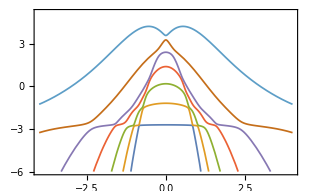
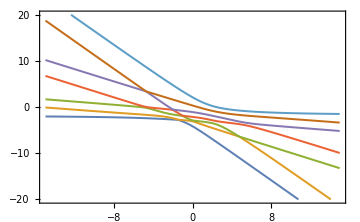

```mathematica
plotOpt={PlotPoints->80,Evaluate@font,ImageSize->Medium,Frame->True,Axes->False,PerformanceGoal->"Quality",PlotStyle->{Thickness[0.004]}};
{plA,plB}={Plot[energies1,{χ,-4,4},PlotRange->{Automatic,{-6,5.2}},Evaluate@plot2,FrameLabel->MaTeX/@{"\\chi","E /Ry"}],
Plot[energies2,{λ,-15,15},PlotRange->{Automatic,{-20,20}},Evaluate@plotOpt,FrameLabel->MaTeX/@{"\\lambda","E /Ry"}]}
```

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=10_energiesl.pdf",plA,"AllowRasterization"->True,ImageSize->330,ImageResolution->800];
Export[NotebookDirectory[]<>"../dp_text/img/N=10_energies2.pdf",plB,"AllowRasterization"->True,ImageSize->320,ImageResolution->800];
```

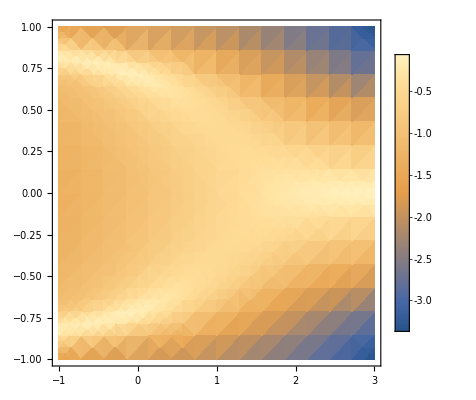

```mathematica
DensityPlot[eigensys[λ,χ][[1,1]]-eigensys[λ,χ][[1,2]],{λ,-1,3},{χ,-1,1},PlotLegends->Automatic]
```

```mathematica
Plot3D[Query[1]@ND[eigensys1[λ,x],{x,2},χ]+Query[1]@ND[eigensys1[l,χ],{l,2},λ],{λ,-3,10},{χ,-1,1},ColorFunction->"SunsetColors",PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
Plot[1-χ^2/(2j)(m+2j)-χ^2 j/2/.{j->4,m->4},{χ,-2,2}]
```

## Symmetries

```mathematica
mirror[listOfVect_]:=Manipulate[Show[{
ListPlot[{ReflectionMatrix[{Cos[θ-π/2],Sin[θ-π/2]}].#},PlotStyle->{{Red,Thickness[0.00001]}},PlotRange->{{-5,5},{-5,5}},AspectRatio->1]&/@listOfVect,
ListPlot[listOfVect],
ListLinePlot[{ {0,0},10{Cos[θ],Sin[θ]}}]
}],{θ,0,π}]
```

```mathematica
eigs=Flatten[Table[Table[{χ,Eigenvalues[HC[1,χ]][[i]]},{χ,-4,4,0.2}],{i,1,7}],1];
```

```mathematica
mirror[eigs]
```

```mathematica
eigsL=Flatten[Table[Table[{λ,Eigenvalues[HC[λ,2]][[i]]},{λ,-4,4,0.2}],{i,1,7}],1];
```

```mathematica
mirror[eigsL]
```

## Degeneracy between all energy levels

## Background

```mathematica
Sp[λ_,χ_]:=Sort[Eigenvalues[H[λ,χ]]];
dSp[λ_,χ_]:=Abs[Sp[λ,χ]⟦1;;dim-1⟧-Sp[λ,χ][[2;;dim]]];
```

```mathematica
difEn=DensityPlot[dSp[λ,χ]⟦#⟧,{λ,-6.5,4.5},{χ,-3.5,3.5},PlotPoints->200,PlotRange->Full,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors",ScalingFunctions->"Log"]&/@Range[dim-1];
```

## Singularities

```mathematica
SpMin=ParallelTable[FindMinimum[{dSp[λ,χ][[#]],χ>-0.01,χ<6,λ<6,λ>-7},{{λ,l},{χ,x}}],{l,-7,5,0.2},{x,-0.2,3,0.2}]&/@Range[dim-1];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

```mathematica
SpMinR[i_]:=Select[Flatten[SpMin[[i]],1],#[[1]]<10^-8&]
```

## Plots

```mathematica
lpl[i_]:=ListPlot[{λ,χ}/.SpMinR[i][[#,2]]&/@Range[Dimensions[SpMinR[i]][[1]]],PlotStyle->{Green,PointSize->0.015}]
layer[i_]:=Show[difEn[[i]],lpl[i]]
```

```mathematica
{layer[1],layer[2],layer[3]}
```

#### N = 7

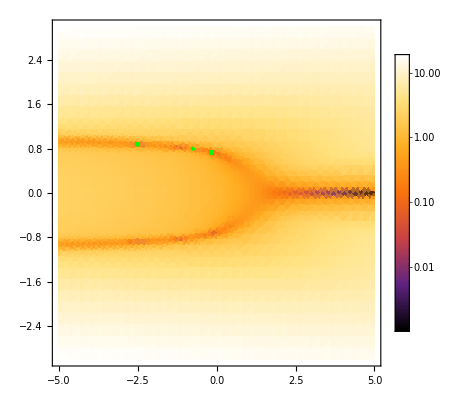
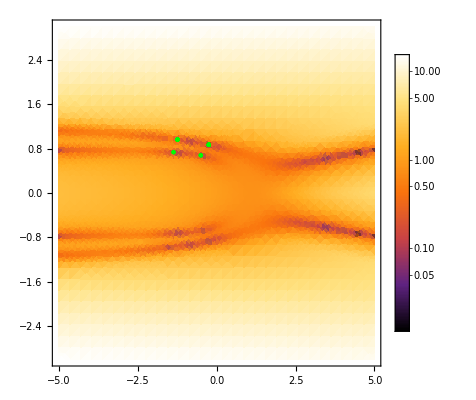
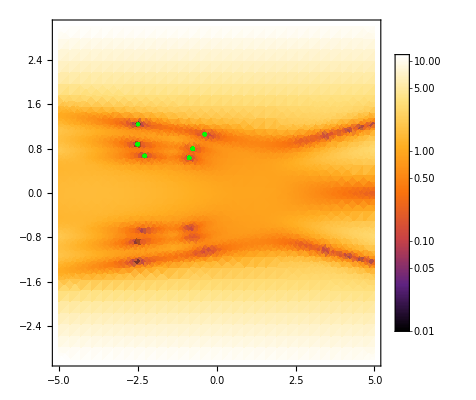
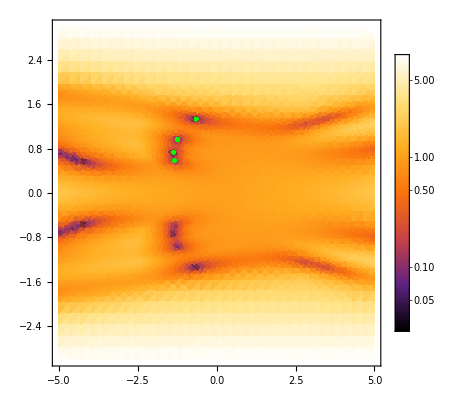
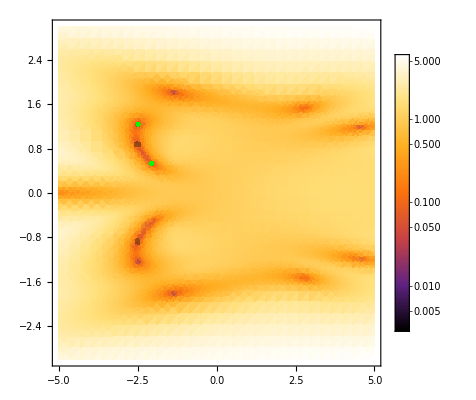
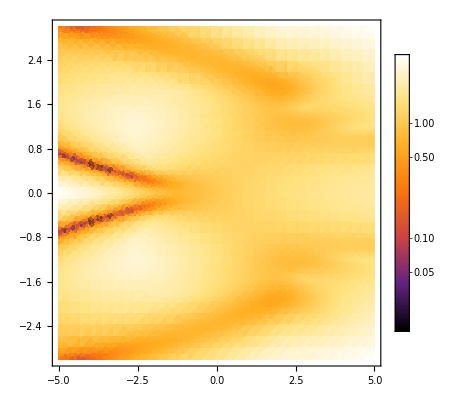
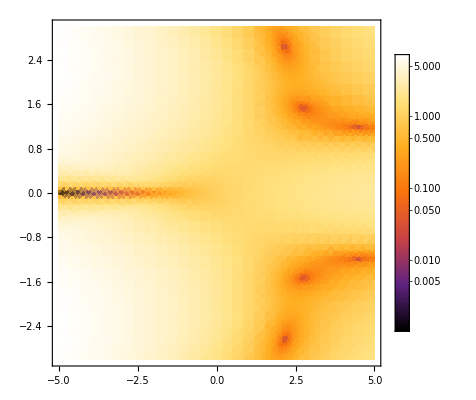

#### N = 6

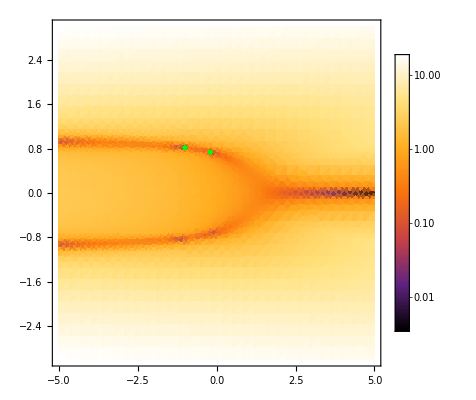
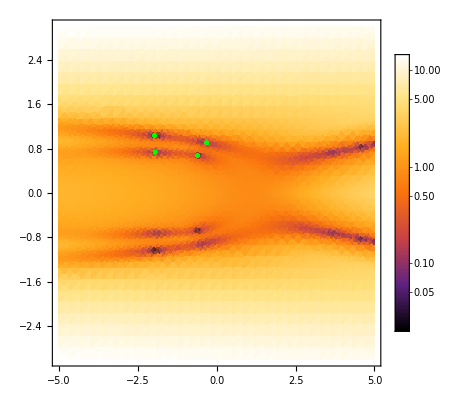
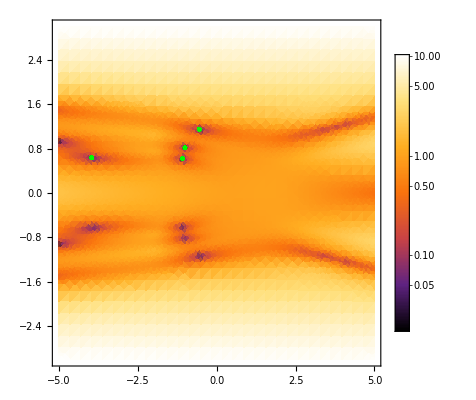
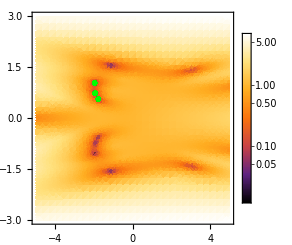
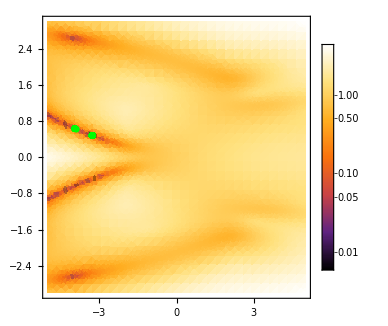
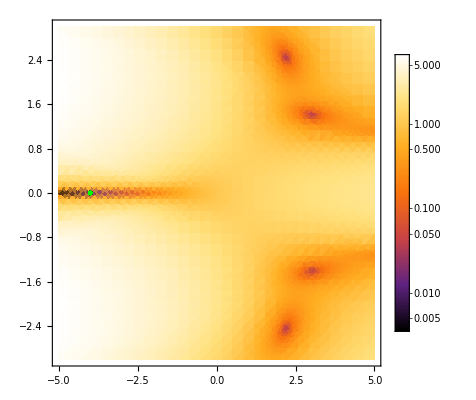

#### N = 5

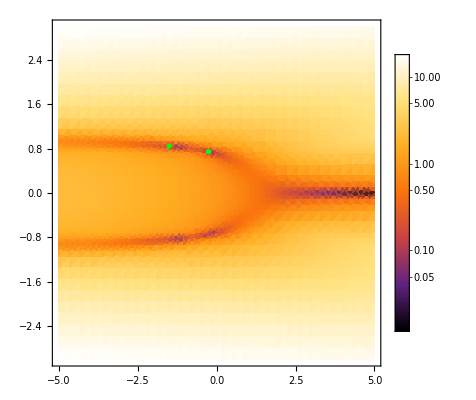
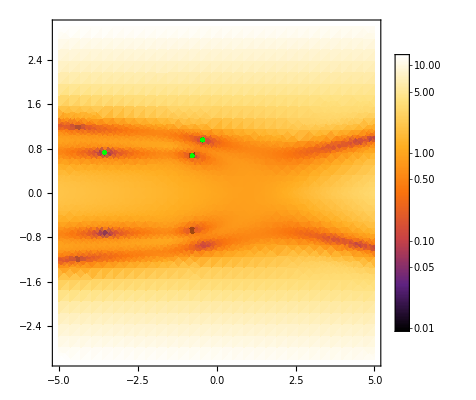
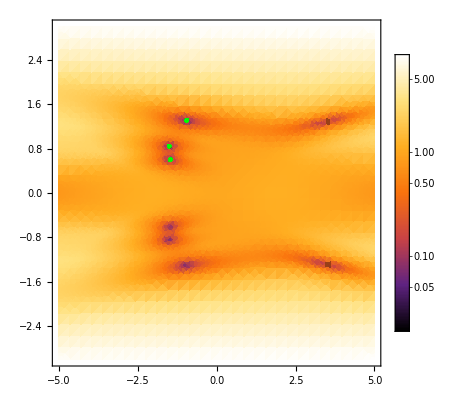
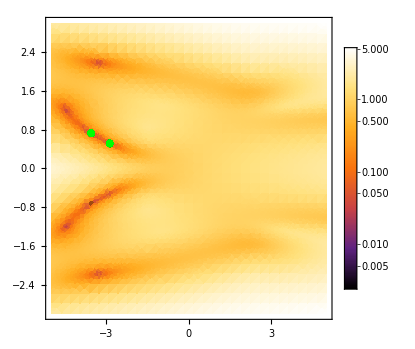
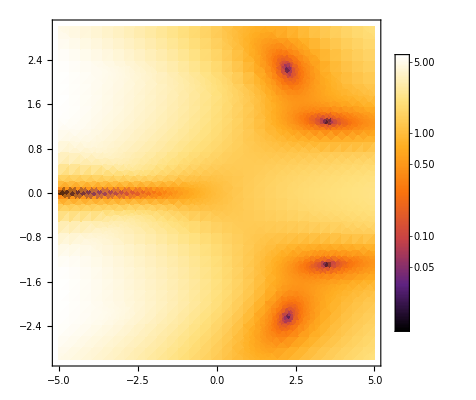

#### N = 4

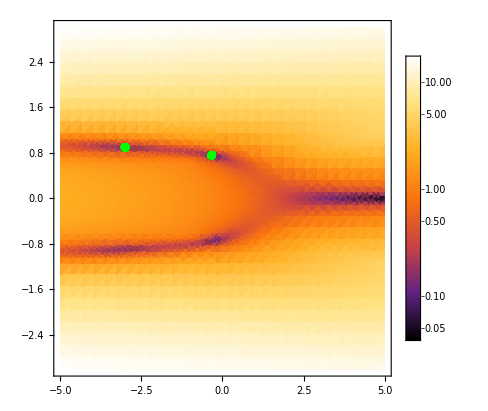
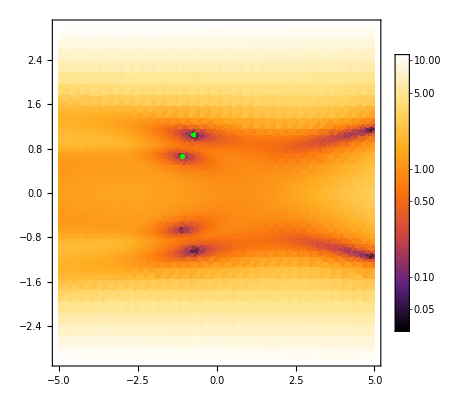
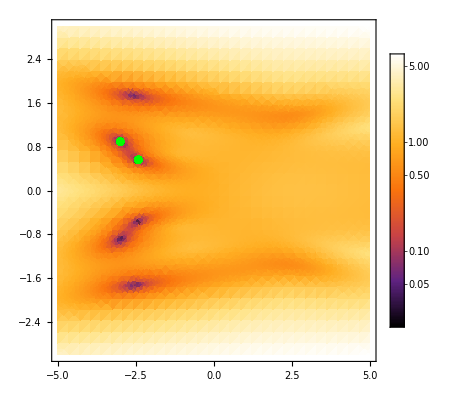
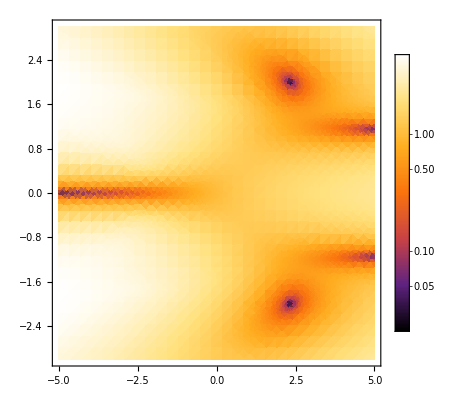

#### N = 3

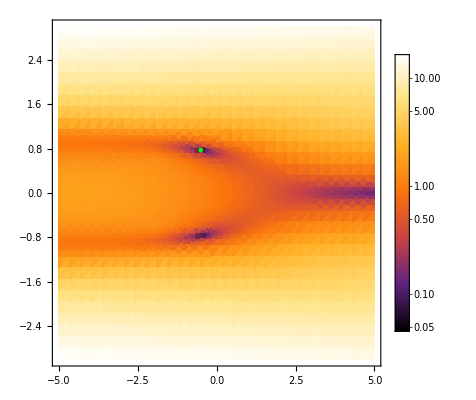
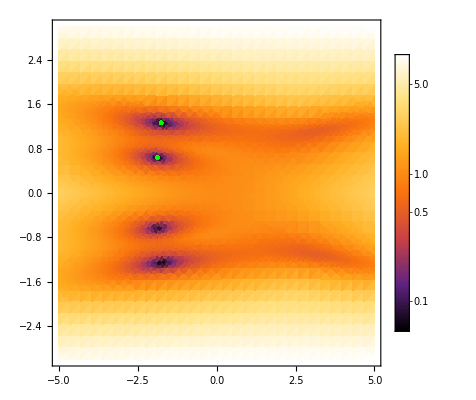
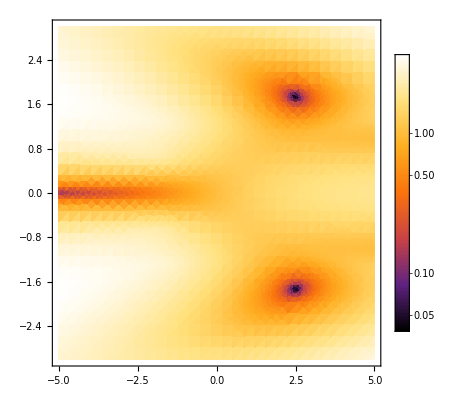

New images of the eigenvalues difference are added from the middle, the characteristics of the first and last images are not N - dependent.

## Example Plot N = 5

### Plot

```mathematica
lpl[i_]:=ListPlot[{{λ,χ},{λ,-χ}}/.SpMinR[i][[#,2]]&/@Range[Dimensions[SpMinR[i]][[1]]],PlotStyle->Blue,PlotMarkers->{cross,0.04}]
layer[i_]:=Show[difEn[[i]],lpl[i]]
```

```mathematica
pt5={
{layer[1],DensityPlot[0,{λ,-6.5,4.5},{χ,-3.5,3.5},PlotRange->Full,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors",ScalingFunctions->"Log"]},
{layer[2],layer[3]},
{layer[4],layer[5]}
};
```

FindMinimum::srect: Value l in search specification {λ,l} is not a number or array of numbers.

General::stop: Further output of FindMinimum::srect will be suppressed during this calculation.

```mathematica
singPlots5=plotGrid[pt5,630/1.4,850/1.4, ImagePadding ->40]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/singularitiesBetweenEnergiesN=6.pdf",singPlots6,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
logTicks[min_,max_]:={#,10^#}&/@FindDivisions[{min,max},5]
bar6=BarLegend[{"SunsetColors",{-3,1}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->420,Ticks->logTicks[-3,1]]
Export[NotebookDirectory[]<>"../dp_text/img/N=5_bar6.pdf",bar6,"AllowRasterization"->True,ImageResolution->800];
```

## Example Plot N = 6

### Plot

```mathematica
lpl[i_]:=ListPlot[{{λ,χ},{λ,-χ}}/.SpMinR[i][[#,2]]&/@Range[Dimensions[SpMinR[i]][[1]]],PlotStyle->Blue,PlotMarkers->{cross,0.04}]
layer[i_]:=Show[difEn[[i]],lpl[i]]
```

```mathematica
pt6={
{layer[1],layer[2]},
{layer[3],layer[4]},
{layer[5],layer[6]}
};
```

```mathematica
singPlots6=plotGrid[pt6,630/1.4,850/1.4, ImagePadding ->40]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/singularitiesBetweenEnergiesN=6.pdf",singPlots6,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
logTicks[min_,max_]:={#,10^#}&/@FindDivisions[{min,max},5]
bar6=BarLegend[{"SunsetColors",{-3,1}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->420,Ticks->logTicks[-3,1]]
Export[NotebookDirectory[]<>"../dp_text/img/N=5_bar6.pdf",bar6,"AllowRasterization"->True,ImageResolution->800];
```

## Singularity dependence on dimension

```mathematica
SpMinArray={};
```

```mathematica
For[nn=3,nn<25,nn++, 
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
Sp[λ_,χ_]:=Sort[Eigenvalues[H[λ,χ]]];
dSp[λ_,χ_]:=Abs[Sp[λ,χ]⟦1;;dim-1⟧-Sp[λ,χ][[2;;dim]]];

min=NMinimize[{dSp[λ,χ][[1]],χ>0.0001,χ<1,λ<1.4,λ>-10,χ^2<(λ-1)/(λ-2)+0.1},{λ,χ},AccuracyGoal->20,PrecisionGoal->20];
AppendTo[SpMinArray,{nn,min}]
]
```

```mathematica
SpMinArray
```

{{3,{0.,{λ→-0.5,χ→0.774597}}},{4,{0.,{λ→-3.,χ→0.894427}}},{5,{0.,{λ→-1.5,χ→0.845154}}},{6,{0.,{λ→-1.,χ→0.816497}}},{7,{0.,{λ→-0.750005,χ→0.797724}}},{8,{0.,{λ→-1.66666,χ→0.852803}}},{9,{7.66396×10^-10,{λ→-3.49996,χ→0.904533}}},{10,{0.,{λ→-2.33339,χ→0.87706}}},{11,{0.,{λ→-1.7499,χ→0.856345}}},{12,{0.,{λ→-1.39967,χ→0.840151}}},{13,{0.,{λ→-2.2503,χ→0.874484}}},{14,{0.,{λ→-3.66765,χ→0.907501}}},{15,{0.,{λ→-2.75956,χ→0.888763}}}}

```mathematica
SpMinPlot=ListPlot[{λ,χ}/.SpMinArray[[#,2,2]]&/@Range[13],PlotStyle->Green];
Show[{det,SpMinPlot}]
```

-Graphics-

```mathematica
cd={λ,χ}/.SpMinArray[[#,2,2]]&/@Range[13]
divPosition=ListPlot[Table[Callout[cd[[i-2]],i],{i,3,15}],Evaluate@font,Frame->True,FrameLabel->MaTeX/@{"\\lambda","\\chi"},ImageSize->Medium];
regr=Plot[√((1-l)/(2-l)),{l,-4,0},PlotStyle->{Gray,Thickness[0.004]}];
divPos=Show[{divPosition,regr}]
```

{{-0.5,0.774597},{-3.,0.894427},{-1.5,0.845154},{-1.,0.816497},{-0.750005,0.797724},{-1.66666,0.852803},{-3.49996,0.904533},{-2.33339,0.87706},{-1.7499,0.856345},{-1.39967,0.840151},{-2.2503,0.874484},{-3.66765,0.907501},{-2.75956,0.888763}}

-Graphics-

## Degeneracy of E0 and E1

## Finding degeneracies using Solve

```mathematica
PrintHamiltonian[3]
```

{{1/4 (-6-λ),-χ/(2 √3),-λ/(2 √3),0},{-χ/(2 √3),1/12 (-6-7 λ-4 χ^2),-χ,-λ/(2 √3)},{-λ/(2 √3),-χ,1/12 (6-7 λ-16 χ^2),-(5 χ)/(2 √3)},{0,-λ/(2 √3),-(5 χ)/(2 √3),3/2-λ/4-3 χ^2}}

```mathematica
degen[nn_]:=Module[{HH,eig2,diff,zeros,SpMinPlot},
HH=PrintHamiltonian[nn];
diff[λ_,χ_]:=Module[{eig},
eig=Sort@Eigenvalues[HH];
eig[[2]]-eig[[1]]
];
zeros=Solve[{diff[λ,χ]==0,χ>0,χ<10,λ<15,λ>-15},{λ,χ}];
SpMinPlot=ListPlot[{λ,χ}/.zeros,PlotStyle->Black,PlotMarkers->✕];

{zeros,Show[{PrintDeterminant[nn,-5,1,0,1.2,20,1,1],SpMinPlot},PlotLabel->StringForm["N="<>ToString@nn]]}
]
```

```mathematica
Timing@degen[8]
```

$Aborted

### Performance of the solver (spoiler: its really slow)

```mathematica
aa=ListPlot[{{1,0.071},{2,0.11},{3,0.457},{4,39.28},{5,264.25},{7,3600*12}}];
```

```mathematica
Manipulate[Show[Plot[a x^10,{x,0,7},PlotRange->All],aa],{{a,0.000148},0.0001,0.001}]
```

Show::gcomb: Could not combine the graphics objects in Show[,aa].

## Results from dimensions 3 to 7

```mathematica
sing = {
{3,{λ->-1/2,χ->√(3/5)}},
{4,{λ->-3,χ->0.8944271909999159},{λ->-0.3333333333333333,χ->0.7559289460184545}},
{5,{λ->-3/2,χ->0.8451542547285166},{λ->-1/4,χ->0.7453559924999299}},
{6,{λ->-5,χ->√(6/7)},{λ->-1,χ->√(2/3)},{λ->-1/5,χ->√(6/11)}},
{7,{λ->-5/2,χ->(√7)/3},{λ->-3/4,χ->√(7/11)},{λ->-1/6,χ->√(7/13)}}
};
```

This corresponds to numerical precision to some beautiful fractions. Number of degeneracies between first and zeroth energy  from first 7 observations corresponds to the array 1,2,2,3,3,...
Spectrum is degenerated in pairs, E1 with E0, E3 with R2,...

```mathematica
singR = {
{3,{λ->-1/2,χ->√(3/5)}},
{4,{λ->-3,χ->√(4/5)},{λ->-1/3,χ->√(4/7)}},
{5,{λ->-3/2,χ->√(5/7)},{λ->-1/4,χ->√(5/9)}},
{6,{λ->-5,χ->√(6/7)},{λ->-1,χ->√(2/3)},{λ->-1/5,χ->√(6/11)}},
{7,{λ->-5/2,χ->√(7/9)},{λ->-3/4,χ->√(7/11)},{λ->-1/6,χ->√(7/13)}},
{8,{λ->-7,χ->√(8/9)},{},{},{λ->-1/7,χ->√(8/15)}},
{9,{λ->-7/2,χ->√(9/11)},{},{},{λ->-1/8,χ->√(9/17)}}
};
```

## Observation leading to general formula

For n even are the first singularities lowest λ) at coordinates (λ,χ)=(1-n/2,√(n/(n+2))), for n even are at (λ,χ)=(1-n,√(n/(n+1)))

Last singularities (highest λ) are at coordinates (λ,χ)=(1/(1-n),√(n/(2n-1)))

```mathematica
sR[n_]:={1/(1-n),√(n/(2n-1))}
sL[n_]:=If[OddQ[n],{1-n/2,√(n/(n+2))},{1-n,√(n/(n+1))}]
```

```mathematica
{sL[3],sL[4],sL[5],sL[6],sL[7]}
```

{{-1/2,√(3/5)},{-3,2/(√5)},{-3/2,√(5/7)},{-5,√(6/7)},{-5/2,(√7)/3}}

```mathematica
CheckSingularityInDim[n_,LR_]:=Module[{eig,coord},
Which[LR=="L",coord=sL[n],LR=="R",coord=sR[n]];
eig = Sort@Eigenvalues[N@PrintHamiltonianV[n,coord]];
If[Abs[eig[[1]]-eig[[2]]]<10^-11,StringJoin[ToString[n]," -> OK"],Style[StringJoin[ToString[n]," -> ΔE = ",ToString[Abs[eig[[1]]-eig[[2]]]]],FontColor->Red]]
]
```

```mathematica
CheckIfLiesOnSeparatrix[x_]:=If[x[[2]]^2==(x[[1]]-1)/(x[[1]]-2),True,Style[False,Red]]
```

```mathematica
sR[6]
```

## Checking formula to n = 500

```mathematica
Table[CheckIfLiesOnSeparatrix[sR[i]],{i,3,500}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
ParallelTable[CheckSingularityInDim[i,"L"],{i,3,500}]
```

{3 -> OK,4 -> OK,5 -> OK,6 -> OK,7 -> OK,8 -> OK,9 -> OK,10 -> OK,11 -> OK,12 -> OK,13 -> OK,14 -> OK,15 -> OK,16 -> OK,17 -> OK,18 -> OK,19 -> OK,20 -> OK,21 -> OK,22 -> OK,23 -> OK,24 -> OK,25 -> OK,26 -> OK,27 -> OK,28 -> OK,29 -> OK,30 -> OK,31 -> OK,32 -> OK,33 -> OK,34 -> OK,35 -> OK,36 -> OK,37 -> OK,38 -> OK,39 -> OK,40 -> OK,41 -> OK,42 -> OK,43 -> OK,44 -> OK,45 -> OK,46 -> OK,47 -> OK,48 -> OK,49 -> OK,50 -> OK,51 -> OK,52 -> OK,53 -> OK,54 -> OK,55 -> OK,56 -> OK,57 -> OK,58 -> OK,59 -> OK,60 -> OK,61 -> OK,62 -> OK,63 -> OK,64 -> OK,65 -> OK,66 -> OK,67 -> OK,68 -> OK,69 -> OK,70 -> OK,71 -> OK,72 -> OK,73 -> OK,74 -> OK,75 -> OK,76 -> OK,77 -> OK,78 -> OK,79 -> OK,80 -> OK,81 -> OK,82 -> OK,83 -> OK,84 -> OK,85 -> OK,86 -> OK,87 -> OK,88 -> OK,89 -> OK,90 -> OK,91 -> OK,92 -> OK,93 -> OK,94 -> OK,95 -> OK,96 -> OK,97 -> OK,98 -> OK,99 -> OK,100 -> OK,101 -> OK,102 -> OK,103 -> OK,104 -> OK,105 -> OK,106 -> OK,107 -> OK,108 -> OK,109 -> OK,110 -> OK,111 -> OK,112 -> OK,113 -> OK,114 -> OK,115 -> OK,116 -> OK,117 -> OK,118 -> OK,119 -> OK,120 -> OK,121 -> OK,122 -> OK,123 -> OK,124 -> OK,125 -> OK,126 -> OK,127 -> OK,128 -> OK,129 -> OK,130 -> OK,131 -> OK,132 -> OK,133 -> OK,134 -> OK,135 -> OK,136 -> OK,137 -> OK,138 -> OK,139 -> OK,140 -> OK,141 -> OK,142 -> OK,143 -> OK,144 -> OK,145 -> OK,146 -> OK,147 -> OK,148 -> OK,149 -> OK,150 -> OK,151 -> OK,152 -> OK,153 -> OK,154 -> OK,155 -> OK,156 -> OK,157 -> OK,158 -> OK,159 -> OK,160 -> OK,161 -> OK,162 -> OK,163 -> OK,164 -> OK,165 -> OK,166 -> OK,167 -> OK,168 -> OK,169 -> OK,170 -> OK,171 -> OK,172 -> OK,173 -> OK,174 -> OK,175 -> OK,176 -> OK,177 -> OK,178 -> OK,179 -> OK,180 -> OK,181 -> OK,182 -> OK,183 -> OK,184 -> OK,185 -> OK,186 -> OK,187 -> OK,188 -> OK,189 -> OK,190 -> OK,191 -> OK,192 -> OK,193 -> OK,194 -> OK,195 -> OK,196 -> OK,197 -> OK,198 -> OK,199 -> OK,200 -> OK,201 -> OK,202 -> OK,203 -> OK,204 -> OK,205 -> OK,206 -> OK,207 -> OK,208 -> OK,209 -> OK,210 -> OK,211 -> OK,212 -> OK,213 -> OK,214 -> OK,215 -> OK,216 -> OK,217 -> OK,218 -> OK,219 -> OK,220 -> OK,221 -> OK,222 -> OK,223 -> OK,224 -> OK,225 -> OK,226 -> OK,227 -> OK,228 -> OK,229 -> OK,230 -> OK,231 -> OK,232 -> OK,233 -> OK,234 -> OK,235 -> OK,236 -> OK,237 -> OK,238 -> OK,239 -> OK,240 -> OK,241 -> OK,242 -> OK,243 -> OK,244 -> OK,245 -> OK,246 -> OK,247 -> OK,248 -> OK,249 -> OK,250 -> OK,251 -> OK,252 -> OK,253 -> OK,254 -> OK,255 -> OK,256 -> OK,257 -> OK,258 -> OK,259 -> OK,260 -> OK,261 -> OK,262 -> OK,263 -> OK,264 -> OK,265 -> OK,266 -> OK,267 -> OK,268 -> OK,269 -> OK,270 -> OK,271 -> OK,272 -> OK,273 -> OK,274 -> OK,275 -> OK,276 -> OK,277 -> OK,278 -> OK,279 -> OK,280 -> OK,281 -> OK,282 -> OK,283 -> OK,284 -> OK,285 -> OK,286 -> OK,287 -> OK,288 -> OK,289 -> OK,290 -> OK,291 -> OK,292 -> OK,293 -> OK,294 -> OK,295 -> OK,296 -> OK,297 -> OK,298 -> OK,299 -> OK,300 -> OK,301 -> OK,302 -> OK,303 -> OK,304 -> OK,305 -> OK,306 -> OK,307 -> OK,308 -> OK,309 -> OK,310 -> OK,311 -> OK,312 -> OK,313 -> OK,314 -> OK,315 -> OK,316 -> OK,317 -> OK,318 -> OK,319 -> OK,320 -> OK,321 -> OK,322 -> OK,323 -> OK,324 -> OK,325 -> OK,326 -> OK,327 -> OK,328 -> OK,329 -> OK,330 -> OK,331 -> OK,332 -> OK,333 -> OK,334 -> OK,335 -> OK,336 -> OK,337 -> OK,338 -> OK,339 -> OK,340 -> OK,341 -> OK,342 -> OK,343 -> OK,344 -> OK,345 -> OK,346 -> OK,347 -> OK,348 -> OK,349 -> OK,350 -> OK,351 -> OK,352 -> OK,353 -> OK,354 -> OK,355 -> OK,356 -> OK,357 -> OK,358 -> OK,359 -> OK,360 -> OK,361 -> OK,362 -> OK,363 -> OK,364 -> OK,365 -> OK,366 -> OK,367 -> OK,368 -> OK,369 -> OK,370 -> OK,371 -> OK,372 -> OK,373 -> OK,374 -> OK,375 -> OK,376 -> OK,377 -> OK,378 -> OK,379 -> OK,380 -> OK,381 -> OK,382 -> OK,383 -> OK,384 -> OK,385 -> OK,386 -> OK,387 -> OK,388 -> OK,389 -> OK,390 -> OK,391 -> OK,392 -> OK,393 -> OK,394 -> OK,395 -> OK,396 -> OK,397 -> OK,398 -> OK,399 -> OK,400 -> OK,401 -> OK,402 -> OK,403 -> OK,404 -> OK,405 -> OK,406 -> OK,407 -> OK,408 -> OK,409 -> OK,410 -> OK,411 -> OK,412 -> OK,413 -> OK,414 -> OK,415 -> OK,416 -> OK,417 -> OK,418 -> OK,419 -> OK,420 -> OK,421 -> OK,422 -> OK,423 -> OK,424 -> OK,425 -> OK,426 -> OK,427 -> OK,428 -> OK,429 -> OK,430 -> OK,431 -> OK,432 -> ΔE =           -11
1.11982 10,433 -> OK,434 -> ΔE =          -11
1.1795 10,435 -> OK,436 -> ΔE =           -11
1.32445 10,437 -> OK,438 -> OK,439 -> OK,440 -> OK,441 -> OK,442 -> OK,443 -> OK,444 -> OK,445 -> OK,446 -> OK,447 -> OK,448 -> OK,449 -> OK,450 -> OK,451 -> OK,452 -> OK,453 -> OK,454 -> OK,455 -> OK,456 -> OK,457 -> OK,458 -> OK,459 -> OK,460 -> OK,461 -> OK,462 -> OK,463 -> OK,464 -> OK,465 -> OK,466 -> OK,467 -> OK,468 -> OK,469 -> OK,470 -> ΔE =           -11
1.37277 10,471 -> OK,472 -> OK,473 -> OK,474 -> OK,475 -> OK,476 -> OK,477 -> OK,478 -> OK,479 -> OK,480 -> OK,481 -> OK,482 -> OK,483 -> OK,484 -> OK,485 -> OK,486 -> OK,487 -> OK,488 -> OK,489 -> OK,490 -> OK,491 -> OK,492 -> OK,493 -> OK,494 -> OK,495 -> OK,496 -> OK,497 -> OK,498 -> OK,499 -> OK,500 -> OK}

```mathematica
ParallelTable[CheckSingularityInDim[i,"R"],{i,3,500}]
```

{3 -> OK,4 -> OK,5 -> OK,6 -> OK,7 -> OK,8 -> OK,9 -> OK,10 -> OK,11 -> OK,12 -> OK,13 -> OK,14 -> OK,15 -> OK,16 -> OK,17 -> OK,18 -> OK,19 -> OK,20 -> OK,21 -> OK,22 -> OK,23 -> OK,24 -> OK,25 -> OK,26 -> OK,27 -> OK,28 -> OK,29 -> OK,30 -> OK,31 -> OK,32 -> OK,33 -> OK,34 -> OK,35 -> OK,36 -> OK,37 -> OK,38 -> OK,39 -> OK,40 -> OK,41 -> OK,42 -> OK,43 -> OK,44 -> OK,45 -> OK,46 -> OK,47 -> OK,48 -> OK,49 -> OK,50 -> OK,51 -> OK,52 -> OK,53 -> OK,54 -> OK,55 -> OK,56 -> OK,57 -> OK,58 -> OK,59 -> OK,60 -> OK,61 -> OK,62 -> OK,63 -> OK,64 -> OK,65 -> OK,66 -> OK,67 -> OK,68 -> OK,69 -> OK,70 -> OK,71 -> OK,72 -> OK,73 -> OK,74 -> OK,75 -> OK,76 -> OK,77 -> OK,78 -> OK,79 -> OK,80 -> OK,81 -> OK,82 -> OK,83 -> OK,84 -> OK,85 -> OK,86 -> OK,87 -> OK,88 -> OK,89 -> OK,90 -> OK,91 -> OK,92 -> OK,93 -> OK,94 -> OK,95 -> OK,96 -> OK,97 -> OK,98 -> OK,99 -> OK,100 -> OK,101 -> OK,102 -> OK,103 -> OK,104 -> OK,105 -> OK,106 -> OK,107 -> OK,108 -> OK,109 -> OK,110 -> OK,111 -> OK,112 -> OK,113 -> OK,114 -> OK,115 -> OK,116 -> OK,117 -> OK,118 -> OK,119 -> OK,120 -> OK,121 -> OK,122 -> OK,123 -> OK,124 -> OK,125 -> OK,126 -> OK,127 -> OK,128 -> OK,129 -> OK,130 -> OK,131 -> OK,132 -> OK,133 -> OK,134 -> OK,135 -> OK,136 -> OK,137 -> OK,138 -> OK,139 -> OK,140 -> OK,141 -> OK,142 -> OK,143 -> OK,144 -> OK,145 -> OK,146 -> OK,147 -> OK,148 -> OK,149 -> OK,150 -> OK,151 -> OK,152 -> OK,153 -> OK,154 -> OK,155 -> OK,156 -> OK,157 -> OK,158 -> OK,159 -> OK,160 -> OK,161 -> OK,162 -> OK,163 -> OK,164 -> OK,165 -> OK,166 -> OK,167 -> OK,168 -> OK,169 -> OK,170 -> OK,171 -> OK,172 -> OK,173 -> OK,174 -> OK,175 -> OK,176 -> OK,177 -> OK,178 -> OK,179 -> OK,180 -> OK,181 -> OK,182 -> OK,183 -> OK,184 -> OK,185 -> OK,186 -> OK,187 -> OK,188 -> OK,189 -> OK,190 -> OK,191 -> OK,192 -> OK,193 -> OK,194 -> OK,195 -> OK,196 -> OK,197 -> OK,198 -> OK,199 -> OK,200 -> OK,201 -> OK,202 -> OK,203 -> OK,204 -> OK,205 -> OK,206 -> OK,207 -> OK,208 -> OK,209 -> OK,210 -> OK,211 -> OK,212 -> OK,213 -> OK,214 -> OK,215 -> OK,216 -> OK,217 -> OK,218 -> OK,219 -> OK,220 -> OK,221 -> OK,222 -> OK,223 -> OK,224 -> OK,225 -> OK,226 -> OK,227 -> OK,228 -> OK,229 -> OK,230 -> OK,231 -> OK,232 -> OK,233 -> OK,234 -> OK,235 -> OK,236 -> OK,237 -> OK,238 -> OK,239 -> OK,240 -> OK,241 -> OK,242 -> OK,243 -> OK,244 -> OK,245 -> OK,246 -> OK,247 -> OK,248 -> OK,249 -> OK,250 -> OK,251 -> OK,252 -> OK,253 -> OK,254 -> OK,255 -> OK,256 -> OK,257 -> OK,258 -> OK,259 -> OK,260 -> OK,261 -> OK,262 -> OK,263 -> OK,264 -> OK,265 -> OK,266 -> OK,267 -> OK,268 -> OK,269 -> OK,270 -> OK,271 -> OK,272 -> OK,273 -> OK,274 -> OK,275 -> OK,276 -> OK,277 -> OK,278 -> OK,279 -> OK,280 -> OK,281 -> OK,282 -> OK,283 -> OK,284 -> OK,285 -> OK,286 -> OK,287 -> OK,288 -> OK,289 -> OK,290 -> OK,291 -> OK,292 -> OK,293 -> OK,294 -> OK,295 -> OK,296 -> OK,297 -> OK,298 -> OK,299 -> OK,300 -> OK,301 -> OK,302 -> OK,303 -> OK,304 -> OK,305 -> OK,306 -> OK,307 -> OK,308 -> OK,309 -> OK,310 -> OK,311 -> OK,312 -> OK,313 -> OK,314 -> OK,315 -> OK,316 -> OK,317 -> OK,318 -> OK,319 -> OK,320 -> OK,321 -> OK,322 -> OK,323 -> OK,324 -> OK,325 -> OK,326 -> OK,327 -> OK,328 -> OK,329 -> OK,330 -> OK,331 -> OK,332 -> OK,333 -> OK,334 -> OK,335 -> OK,336 -> OK,337 -> OK,338 -> OK,339 -> OK,340 -> OK,341 -> OK,342 -> OK,343 -> OK,344 -> OK,345 -> OK,346 -> OK,347 -> OK,348 -> OK,349 -> OK,350 -> OK,351 -> OK,352 -> OK,353 -> OK,354 -> OK,355 -> OK,356 -> OK,357 -> OK,358 -> OK,359 -> OK,360 -> OK,361 -> OK,362 -> OK,363 -> OK,364 -> OK,365 -> OK,366 -> OK,367 -> OK,368 -> OK,369 -> OK,370 -> OK,371 -> OK,372 -> OK,373 -> OK,374 -> OK,375 -> OK,376 -> OK,377 -> OK,378 -> OK,379 -> OK,380 -> OK,381 -> OK,382 -> OK,383 -> OK,384 -> OK,385 -> OK,386 -> OK,387 -> OK,388 -> OK,389 -> OK,390 -> OK,391 -> OK,392 -> OK,393 -> OK,394 -> OK,395 -> OK,396 -> OK,397 -> OK,398 -> OK,399 -> OK,400 -> OK,401 -> OK,402 -> OK,403 -> OK,404 -> OK,405 -> OK,406 -> OK,407 -> OK,408 -> OK,409 -> OK,410 -> OK,411 -> OK,412 -> OK,413 -> OK,414 -> OK,415 -> OK,416 -> OK,417 -> OK,418 -> OK,419 -> OK,420 -> OK,421 -> OK,422 -> OK,423 -> OK,424 -> OK,425 -> OK,426 -> OK,427 -> OK,428 -> OK,429 -> OK,430 -> OK,431 -> OK,432 -> OK,433 -> OK,434 -> OK,435 -> OK,436 -> OK,437 -> OK,438 -> OK,439 -> OK,440 -> OK,441 -> OK,442 -> OK,443 -> OK,444 -> OK,445 -> OK,446 -> OK,447 -> OK,448 -> OK,449 -> OK,450 -> OK,451 -> OK,452 -> OK,453 -> OK,454 -> OK,455 -> OK,456 -> OK,457 -> OK,458 -> OK,459 -> OK,460 -> OK,461 -> OK,462 -> OK,463 -> OK,464 -> OK,465 -> OK,466 -> OK,467 -> OK,468 -> OK,469 -> OK,470 -> OK,471 -> OK,472 -> OK,473 -> OK,474 -> OK,475 -> OK,476 -> OK,477 -> OK,478 -> OK,479 -> OK,480 -> OK,481 -> OK,482 -> OK,483 -> OK,484 -> OK,485 -> OK,486 -> OK,487 -> OK,488 -> OK,489 -> OK,490 -> OK,491 -> OK,492 -> OK,493 -> OK,494 -> OK,495 -> OK,496 -> OK,497 -> OK,498 -> OK,499 -> OK,500 -> OK}

```mathematica
ParallelTable[CheckSingularityInDim[i,"L"],{i,501,1000}]
```

{501 -> OK,502 -> ΔE =           -11
1.18234 10,503 -> OK,504 -> OK,505 -> OK,506 -> OK,507 -> OK,508 -> ΔE =           -11
1.01181 10,509 -> OK,510 -> OK,511 -> OK,512 -> OK,513 -> OK,514 -> OK,515 -> OK,516 -> ΔE =           -11
1.16529 10,517 -> OK,518 -> ΔE =           -11
1.54046 10,519 -> OK,520 -> ΔE =          -11
1.5774 10,521 -> OK,522 -> OK,523 -> OK,524 -> OK,525 -> OK,526 -> ΔE =           -11
1.06866 10,527 -> OK,528 -> ΔE =           -11
1.43814 10,529 -> ΔE =           -11
1.02318 10,530 -> OK,531 -> OK,532 -> OK,533 -> OK,534 -> OK,535 -> OK,536 -> OK,537 -> OK,538 -> OK,539 -> OK,540 -> OK,541 -> OK,542 -> OK,543 -> ΔE =           -11
1.40403 10,544 -> OK,545 -> OK,546 -> ΔE =           -11
1.64277 10,547 -> OK,548 -> OK,549 -> ΔE =           -11
1.73941 10,550 -> OK,551 -> OK,552 -> OK,553 -> OK,554 -> OK,555 -> OK,556 -> OK,557 -> OK,558 -> OK,559 -> OK,560 -> OK,561 -> OK,562 -> ΔE =           -11
1.31308 10,563 -> OK,564 -> ΔE =           -11
1.22213 10,565 -> OK,566 -> OK,567 -> OK,568 -> OK,569 -> OK,570 -> OK,571 -> ΔE =           -11
1.54046 10,572 -> OK,573 -> OK,574 -> OK,575 -> OK,576 -> OK,577 -> OK,578 -> OK,579 -> OK,580 -> OK,581 -> OK,582 -> OK,583 -> OK,584 -> ΔE =           -11
1.31877 10,585 -> OK,586 -> ΔE =           -11
2.53522 10,587 -> OK,588 -> OK,589 -> OK,590 -> OK,591 -> ΔE =           -11
1.07434 10,592 -> OK,593 -> OK,594 -> OK,595 -> OK,596 -> OK,597 -> OK,598 -> OK,599 -> OK,600 -> OK,601 -> OK,602 -> OK,603 -> ΔE =           -11
1.02887 10,604 -> OK,605 -> ΔE =           -11
1.03455 10,606 -> OK,607 -> ΔE =           -11
1.80762 10,608 -> ΔE =          -11
1.3074 10,609 -> OK,610 -> OK,611 -> OK,612 -> ΔE =           -11
1.64277 10,613 -> OK,614 -> OK,615 -> OK,616 -> ΔE =           -11
2.47837 10,617 -> OK,618 -> OK,619 -> OK,620 -> OK,621 -> OK,622 -> OK,623 -> OK,624 -> ΔE =           -11
2.62048 10,625 -> OK,626 -> OK,627 -> OK,628 -> ΔE =           -11
1.44951 10,629 -> OK,630 -> ΔE =          -11
1.5973 10,631 -> OK,632 -> OK,633 -> OK,634 -> ΔE =           -11
2.31353 10,635 -> OK,636 -> OK,637 -> OK,638 -> OK,639 -> OK,640 -> OK,641 -> OK,642 -> ΔE =           -11
1.42109 10,643 -> OK,644 -> OK,645 -> OK,646 -> ΔE =           -11
1.06297 10,647 -> OK,648 -> OK,649 -> OK,650 -> OK,651 -> OK,652 -> OK,653 -> OK,654 -> OK,655 -> OK,656 -> ΔE =           -11
2.27374 10,657 -> ΔE =           -11
1.46656 10,658 -> ΔE =           -11
1.35856 10,659 -> ΔE =          -11
1.0516 10,660 -> OK,661 -> OK,662 -> OK,663 -> OK,664 -> ΔE =           -11
1.29035 10,665 -> OK,666 -> OK,667 -> OK,668 -> OK,669 -> OK,670 -> OK,671 -> OK,672 -> ΔE =           -11
1.40972 10,673 -> OK,674 -> OK,675 -> OK,676 -> ΔE =           -11
1.04592 10,677 -> OK,678 -> ΔE =           -11
1.08002 10,679 -> ΔE =           -11
1.04592 10,680 -> OK,681 -> OK,682 -> ΔE =           -11
2.10321 10,683 -> OK,684 -> OK,685 -> OK,686 -> OK,687 -> OK,688 -> ΔE =           -11
1.78488 10,689 -> OK,690 -> ΔE =           -11
1.68825 10,691 -> ΔE =           -11
1.26192 10,692 -> ΔE =           -11
2.25668 10,693 -> OK,694 -> OK,695 -> OK,696 -> OK,697 -> OK,698 -> OK,699 -> OK,700 -> OK,701 -> OK,702 -> ΔE =           -11
2.15437 10,703 -> OK,704 -> OK,705 -> ΔE =           -11
1.13118 10,706 -> ΔE =           -11
1.09708 10,707 -> OK,708 -> OK,709 -> OK,710 -> ΔE =           -11
1.27329 10,711 -> OK,712 -> ΔE =           -11
1.60867 10,713 -> OK,714 -> ΔE =           -11
1.24487 10,715 -> OK,716 -> OK,717 -> ΔE =           -11
1.14824 10,718 -> ΔE =           -11
2.23395 10,719 -> OK,720 -> ΔE =           -11
1.60298 10,721 -> ΔE =          -11
1.1994 10,722 -> OK,723 -> OK,724 -> ΔE =           -11
1.31877 10,725 -> ΔE =           -11
2.11458 10,726 -> ΔE =           -11
1.71099 10,727 -> ΔE =           -11
1.62572 10,728 -> OK,729 -> ΔE =           -11
1.40403 10,730 -> ΔE =           -11
2.58638 10,731 -> OK,732 -> OK,733 -> OK,734 -> ΔE =           -11
1.51772 10,735 -> OK,736 -> OK,737 -> OK,738 -> OK,739 -> ΔE =           -11
1.28466 10,740 -> OK,741 -> OK,742 -> OK,743 -> OK,744 -> ΔE =           -11
1.53477 10,745 -> OK,746 -> ΔE =          -11
1.0175 10,747 -> ΔE =           -11
1.53477 10,748 -> OK,749 -> OK,750 -> OK,751 -> OK,752 -> ΔE =           -11
1.62572 10,753 -> ΔE =           -11
1.08571 10,754 -> OK,755 -> ΔE =           -11
1.14255 10,756 -> ΔE =           -11
1.88152 10,757 -> OK,758 -> ΔE =           -11
1.64277 10,759 -> OK,760 -> OK,761 -> OK,762 -> ΔE =           -11
1.87583 10,763 -> OK,764 -> ΔE =           -11
2.46132 10,765 -> OK,766 -> OK,767 -> OK,768 -> ΔE =           -11
2.51816 10,769 -> OK,770 -> OK,771 -> OK,772 -> ΔE =           -11
1.63141 10,773 -> ΔE =           -11
1.14255 10,774 -> ΔE =           -11
2.22258 10,775 -> ΔE =           -11
1.15961 10,776 -> OK,777 -> OK,778 -> OK,779 -> OK,780 -> OK,781 -> ΔE =           -11
1.00044 10,782 -> ΔE =           -11
1.95541 10,783 -> OK,784 -> ΔE =           -11
3.32534 10,785 -> OK,786 -> OK,787 -> OK,788 -> OK,789 -> OK,790 -> ΔE =           -11
1.30171 10,791 -> OK,792 -> ΔE =          -11
1.1255 10,793 -> OK,794 -> ΔE =           -11
1.79057 10,795 -> OK,796 -> ΔE =           -11
1.89289 10,797 -> OK,798 -> OK,799 -> OK,800 -> ΔE =           -11
1.90425 10,801 -> OK,802 -> OK,803 -> OK,804 -> ΔE =           -11
2.63185 10,805 -> OK,806 -> ΔE =           -11
2.09752 10,807 -> OK,808 -> ΔE =           -11
3.41629 10,809 -> OK,810 -> ΔE =           -11
2.89333 10,811 -> OK,812 -> ΔE =           -11
1.26761 10,813 -> OK,814 -> ΔE =           -11
3.86535 10,815 -> ΔE =           -11
1.10276 10,816 -> ΔE =           -11
2.71143 10,817 -> OK,818 -> OK,819 -> OK,820 -> ΔE =           -11
1.35856 10,821 -> ΔE =           -11
1.26192 10,822 -> OK,823 -> OK,824 -> OK,825 -> OK,826 -> ΔE =           -11
1.24487 10,827 -> ΔE =           -11
1.42677 10,828 -> OK,829 -> OK,830 -> ΔE =           -11
2.52953 10,831 -> OK,832 -> OK,833 -> OK,834 -> ΔE =           -11
1.01181 10,835 -> OK,836 -> ΔE =           -11
3.20597 10,837 -> ΔE =           -11
1.21076 10,838 -> ΔE =           -11
1.73941 10,839 -> OK,840 -> OK,841 -> OK,842 -> OK,843 -> OK,844 -> ΔE =           -11
2.75691 10,845 -> ΔE =           -11
1.38698 10,846 -> ΔE =           -11
2.84217 10,847 -> OK,848 -> ΔE =           -11
1.71667 10,849 -> OK,850 -> ΔE =           -11
1.06297 10,851 -> OK,852 -> ΔE =           -11
1.36993 10,853 -> OK,854 -> ΔE =           -11
2.63753 10,855 -> ΔE =           -11
3.00133 10,856 -> OK,857 -> OK,858 -> ΔE =           -11
2.18847 10,859 -> ΔE =           -11
2.67164 10,860 -> ΔE =           -11
2.84217 10,861 -> OK,862 -> ΔE =           -11
2.96723 10,863 -> ΔE =           -11
1.81899 10,864 -> ΔE =           -11
1.65414 10,865 -> OK,866 -> ΔE =           -11
4.66684 10,867 -> OK,868 -> ΔE =           -11
1.40972 10,869 -> ΔE =           -11
1.09708 10,870 -> ΔE =           -11
1.23919 10,871 -> OK,872 -> ΔE =           -11
3.44471 10,873 -> ΔE =          -11
2.6489 10,874 -> ΔE =           -11
4.43379 10,875 -> ΔE =           -11
2.81943 10,876 -> ΔE =           -11
1.26192 10,877 -> OK,878 -> ΔE =           -11
1.23919 10,879 -> OK,880 -> ΔE =           -11
1.15961 10,881 -> ΔE =           -11
1.33014 10,882 -> OK,883 -> OK,884 -> ΔE =           -11
1.91562 10,885 -> OK,886 -> ΔE =           -11
3.13207 10,887 -> OK,888 -> ΔE =           -11
1.54614 10,889 -> OK,890 -> ΔE =           -11
2.03499 10,891 -> OK,892 -> ΔE =           -11
2.18279 10,893 -> OK,894 -> ΔE =           -11
2.12594 10,895 -> ΔE =           -11
2.02931 10,896 -> OK,897 -> ΔE =          -11
1.4893 10,898 -> OK,899 -> ΔE =           -11
2.75122 10,900 -> OK,901 -> ΔE =           -11
1.10845 10,902 -> OK,903 -> ΔE =           -11
1.78488 10,904 -> OK,905 -> OK,906 -> ΔE =           -11
1.08571 10,907 -> OK,908 -> ΔE =           -11
4.38263 10,909 -> OK,910 -> ΔE =           -11
4.39968 10,911 -> ΔE =           -11
2.91038 10,912 -> ΔE =           -11
1.76215 10,913 -> ΔE =           -11
1.56319 10,914 -> ΔE =           -11
2.09184 10,915 -> OK,916 -> ΔE =           -11
3.00702 10,917 -> ΔE =           -11
2.07478 10,918 -> OK,919 -> ΔE =           -11
3.25144 10,920 -> ΔE =           -11
2.01226 10,921 -> ΔE =           -11
1.83036 10,922 -> ΔE =           -11
2.02931 10,923 -> ΔE =           -11
1.57456 10,924 -> OK,925 -> ΔE =           -11
1.28466 10,926 -> ΔE =           -11
1.18234 10,927 -> OK,928 -> OK,929 -> ΔE =           -11
3.56408 10,930 -> ΔE =           -11
2.77964 10,931 -> OK,932 -> OK,933 -> ΔE =           -11
1.09139 10,934 -> ΔE =           -11
2.68301 10,935 -> ΔE =           -11
3.93925 10,936 -> ΔE =           -11
4.09841 10,937 -> ΔE =           -11
2.29079 10,938 -> OK,939 -> ΔE =           -11
1.92131 10,940 -> ΔE =           -11
2.66596 10,941 -> ΔE =           -11
2.70575 10,942 -> ΔE =           -11
2.87059 10,943 -> OK,944 -> ΔE =           -11
2.81375 10,945 -> ΔE =          -11
1.3415 10,946 -> ΔE =           -11
2.89333 10,947 -> OK,948 -> OK,949 -> ΔE =          -11
2.3249 10,950 -> ΔE =           -11
4.64411 10,951 -> OK,952 -> OK,953 -> OK,954 -> ΔE =           -11
2.52953 10,955 -> ΔE =           -11
2.00657 10,956 -> ΔE =           -11
1.39266 10,957 -> ΔE =           -11
1.17097 10,958 -> ΔE =           -11
1.14824 10,959 -> ΔE =          -11
1.5234 10,960 -> ΔE =           -11
1.76783 10,961 -> OK,962 -> ΔE =           -11
1.97247 10,963 -> ΔE =           -11
1.73372 10,964 -> ΔE =           -11
1.74509 10,965 -> OK,966 -> ΔE =           -11
2.91607 10,967 -> ΔE =          -11
1.5973 10,968 -> ΔE =           -11
2.93312 10,969 -> OK,970 -> ΔE =           -11
4.34852 10,971 -> ΔE =           -11
1.50635 10,972 -> ΔE =           -11
4.51337 10,973 -> ΔE =          -11
1.0516 10,974 -> ΔE =           -11
2.09752 10,975 -> OK,976 -> ΔE =          -11
1.3813 10,977 -> OK,978 -> ΔE =           -11
2.27942 10,979 -> OK,980 -> ΔE =           -11
2.19984 10,981 -> ΔE =           -11
1.01181 10,982 -> ΔE =           -11
2.01794 10,983 -> OK,984 -> ΔE =           -11
3.33102 10,985 -> OK,986 -> OK,987 -> ΔE =           -11
1.33014 10,988 -> ΔE =           -11
5.83782 10,989 -> ΔE =           -11
2.41585 10,990 -> ΔE =           -11
4.41673 10,991 -> ΔE =          -11
3.0866 10,992 -> ΔE =           -11
1.84173 10,993 -> OK,994 -> ΔE =           -11
2.38174 10,995 -> ΔE =           -11
1.54046 10,996 -> ΔE =           -11
2.27374 10,997 -> OK,998 -> ΔE =           -11
1.56888 10,999 -> OK,1000 -> ΔE =          -11
7.2248 10}

```mathematica
ParallelTable[CheckSingularityInDim[i,"R"],{i,501,1000}]
```

{501 -> OK,502 -> OK,503 -> OK,504 -> OK,505 -> OK,506 -> OK,507 -> OK,508 -> OK,509 -> OK,510 -> OK,511 -> OK,512 -> OK,513 -> OK,514 -> OK,515 -> OK,516 -> OK,517 -> OK,518 -> OK,519 -> OK,520 -> OK,521 -> OK,522 -> OK,523 -> OK,524 -> OK,525 -> OK,526 -> OK,527 -> OK,528 -> OK,529 -> OK,530 -> OK,531 -> OK,532 -> OK,533 -> OK,534 -> OK,535 -> OK,536 -> OK,537 -> OK,538 -> OK,539 -> OK,540 -> OK,541 -> OK,542 -> OK,543 -> OK,544 -> OK,545 -> OK,546 -> OK,547 -> OK,548 -> OK,549 -> OK,550 -> OK,551 -> OK,552 -> OK,553 -> OK,554 -> OK,555 -> OK,556 -> OK,557 -> OK,558 -> OK,559 -> OK,560 -> OK,561 -> OK,562 -> OK,563 -> OK,564 -> OK,565 -> OK,566 -> OK,567 -> OK,568 -> OK,569 -> OK,570 -> OK,571 -> OK,572 -> OK,573 -> OK,574 -> OK,575 -> OK,576 -> OK,577 -> OK,578 -> OK,579 -> OK,580 -> OK,581 -> OK,582 -> OK,583 -> OK,584 -> OK,585 -> OK,586 -> OK,587 -> OK,588 -> OK,589 -> OK,590 -> OK,591 -> OK,592 -> OK,593 -> OK,594 -> OK,595 -> OK,596 -> OK,597 -> OK,598 -> OK,599 -> OK,600 -> OK,601 -> OK,602 -> OK,603 -> OK,604 -> OK,605 -> OK,606 -> OK,607 -> OK,608 -> OK,609 -> OK,610 -> OK,611 -> OK,612 -> OK,613 -> OK,614 -> OK,615 -> OK,616 -> OK,617 -> OK,618 -> OK,619 -> OK,620 -> OK,621 -> OK,622 -> OK,623 -> OK,624 -> OK,625 -> OK,626 -> OK,627 -> OK,628 -> OK,629 -> OK,630 -> OK,631 -> OK,632 -> OK,633 -> OK,634 -> OK,635 -> OK,636 -> OK,637 -> OK,638 -> OK,639 -> OK,640 -> OK,641 -> OK,642 -> OK,643 -> OK,644 -> OK,645 -> OK,646 -> OK,647 -> OK,648 -> OK,649 -> OK,650 -> OK,651 -> OK,652 -> OK,653 -> OK,654 -> OK,655 -> OK,656 -> OK,657 -> OK,658 -> OK,659 -> OK,660 -> OK,661 -> OK,662 -> OK,663 -> OK,664 -> OK,665 -> OK,666 -> OK,667 -> OK,668 -> OK,669 -> OK,670 -> OK,671 -> OK,672 -> OK,673 -> OK,674 -> OK,675 -> OK,676 -> OK,677 -> OK,678 -> OK,679 -> OK,680 -> OK,681 -> OK,682 -> OK,683 -> OK,684 -> OK,685 -> OK,686 -> OK,687 -> OK,688 -> OK,689 -> OK,690 -> OK,691 -> OK,692 -> OK,693 -> OK,694 -> OK,695 -> OK,696 -> OK,697 -> OK,698 -> OK,699 -> OK,700 -> OK,701 -> OK,702 -> OK,703 -> OK,704 -> OK,705 -> OK,706 -> OK,707 -> OK,708 -> OK,709 -> OK,710 -> OK,711 -> OK,712 -> OK,713 -> OK,714 -> OK,715 -> OK,716 -> OK,717 -> OK,718 -> OK,719 -> OK,720 -> OK,721 -> OK,722 -> OK,723 -> OK,724 -> OK,725 -> OK,726 -> OK,727 -> OK,728 -> OK,729 -> OK,730 -> OK,731 -> OK,732 -> OK,733 -> OK,734 -> OK,735 -> OK,736 -> OK,737 -> OK,738 -> OK,739 -> OK,740 -> OK,741 -> OK,742 -> OK,743 -> OK,744 -> OK,745 -> OK,746 -> OK,747 -> OK,748 -> OK,749 -> OK,750 -> OK,751 -> OK,752 -> OK,753 -> OK,754 -> OK,755 -> OK,756 -> OK,757 -> OK,758 -> OK,759 -> OK,760 -> OK,761 -> OK,762 -> OK,763 -> OK,764 -> OK,765 -> OK,766 -> OK,767 -> OK,768 -> OK,769 -> OK,770 -> OK,771 -> OK,772 -> OK,773 -> OK,774 -> OK,775 -> OK,776 -> OK,777 -> OK,778 -> OK,779 -> OK,780 -> OK,781 -> OK,782 -> OK,783 -> OK,784 -> OK,785 -> OK,786 -> OK,787 -> OK,788 -> OK,789 -> OK,790 -> OK,791 -> OK,792 -> OK,793 -> OK,794 -> OK,795 -> OK,796 -> OK,797 -> OK,798 -> OK,799 -> OK,800 -> OK,801 -> OK,802 -> OK,803 -> OK,804 -> OK,805 -> OK,806 -> OK,807 -> OK,808 -> OK,809 -> OK,810 -> OK,811 -> OK,812 -> OK,813 -> OK,814 -> OK,815 -> OK,816 -> OK,817 -> OK,818 -> OK,819 -> OK,820 -> OK,821 -> OK,822 -> OK,823 -> OK,824 -> OK,825 -> OK,826 -> OK,827 -> OK,828 -> OK,829 -> OK,830 -> OK,831 -> OK,832 -> OK,833 -> OK,834 -> OK,835 -> OK,836 -> OK,837 -> OK,838 -> OK,839 -> OK,840 -> OK,841 -> OK,842 -> OK,843 -> OK,844 -> OK,845 -> OK,846 -> OK,847 -> OK,848 -> OK,849 -> OK,850 -> OK,851 -> OK,852 -> OK,853 -> OK,854 -> OK,855 -> OK,856 -> OK,857 -> OK,858 -> OK,859 -> OK,860 -> OK,861 -> OK,862 -> OK,863 -> OK,864 -> OK,865 -> OK,866 -> OK,867 -> OK,868 -> OK,869 -> OK,870 -> OK,871 -> OK,872 -> OK,873 -> OK,874 -> OK,875 -> OK,876 -> OK,877 -> OK,878 -> OK,879 -> OK,880 -> OK,881 -> OK,882 -> OK,883 -> OK,884 -> OK,885 -> OK,886 -> OK,887 -> OK,888 -> OK,889 -> OK,890 -> OK,891 -> OK,892 -> OK,893 -> OK,894 -> OK,895 -> OK,896 -> OK,897 -> OK,898 -> OK,899 -> OK,900 -> OK,901 -> OK,902 -> OK,903 -> OK,904 -> OK,905 -> OK,906 -> OK,907 -> OK,908 -> OK,909 -> OK,910 -> OK,911 -> OK,912 -> OK,913 -> OK,914 -> OK,915 -> OK,916 -> OK,917 -> OK,918 -> OK,919 -> OK,920 -> OK,921 -> OK,922 -> OK,923 -> OK,924 -> OK,925 -> OK,926 -> OK,927 -> OK,928 -> OK,929 -> OK,930 -> OK,931 -> OK,932 -> OK,933 -> OK,934 -> OK,935 -> OK,936 -> OK,937 -> OK,938 -> OK,939 -> OK,940 -> OK,941 -> OK,942 -> OK,943 -> OK,944 -> OK,945 -> OK,946 -> OK,947 -> OK,948 -> OK,949 -> OK,950 -> OK,951 -> OK,952 -> OK,953 -> OK,954 -> OK,955 -> OK,956 -> OK,957 -> OK,958 -> OK,959 -> OK,960 -> OK,961 -> OK,962 -> OK,963 -> OK,964 -> OK,965 -> OK,966 -> OK,967 -> OK,968 -> OK,969 -> OK,970 -> OK,971 -> OK,972 -> OK,973 -> OK,974 -> OK,975 -> OK,976 -> OK,977 -> OK,978 -> OK,979 -> OK,980 -> OK,981 -> OK,982 -> OK,983 -> OK,984 -> OK,985 -> OK,986 -> OK,987 -> OK,988 -> OK,989 -> OK,990 -> OK,991 -> OK,992 -> OK,993 -> OK,994 -> OK,995 -> OK,996 -> OK,997 -> OK,998 -> OK,999 -> OK,1000 -> OK}

## Plotting singularity coordinates on the determinant background

```mathematica
PrintPlotForGrid[n_,sw_]:=Show[PrintDeterminant[n,-10,1,-0.02,1.05,200,0,sw],ListPlot[{sL[n]},PlotStyle->Black,PlotMarkers->{cross,0.04}],ListPlot[{sR[n]},PlotStyle->Black,PlotMarkers->{cross,0.04}]]
```

```mathematica
pt={
{PrintPlotForGrid[3,1],PrintPlotForGrid[4,0]},
{PrintPlotForGrid[5,1],PrintPlotForGrid[6,0]},
{PrintPlotForGrid[7,1],PrintPlotForGrid[8,0]},
{PrintPlotForGrid[9,1],PrintPlotForGrid[10,0]}
};
```

```mathematica
singPlots=plotGrid[pt,560/1.4,900/1.4, ImagePadding ->40]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/singularitiesPlots.pdf",singPlots,"AllowRasterization"->True,ImageResolution->800];
```

# Plotting some geometrical stuff

## Metric tensor

```mathematica
optDen={Evaluate@densityPlotOptions,PlotPoints->20,ImageSize->Medium};
{DensityPlot[ArcTan[gC[y,x]⟦1,1⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gC[y,x]⟦2,2⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gC[y,x]⟦1,2⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen]}
```

{-Graphics-,-Graphics-,-Graphics-}

#### Metric tensor determinant

```mathematica
DensityPlot[Det[gC[x,l]],{x,0,2.5},{l,0,2},Evaluate@densityPlotOptions,PlotPoints->300,ScalingFunctions->"Log10",PlotRange->Full]
```

-Graphics-

```mathematica
det3D=Plot3D[Det[gC[l,x]],{l,-5,5},{x,0,1.5},PlotPoints->150,Evaluate@font,ScalingFunctions->"Log10", ColorFunction->"SunsetColors",AxesLabel->MaTeX/@{"\\lambda","\\chi","Det(g)"},Ticks->{{-5,-2.5,0,2.5,5},{0,0.5,1,1.5},Table[{10^k,Superscript[10,k]},{k,-5,5,3}]},TicksStyle->"LogTicks"]
```

-Graphics3D-

```mathematica
detgλ=DensityPlot[ArcTan@Det[ND[gC[l,χ],l,λ]],{λ,-5,5},{χ,0,1.2},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->150,PlotRange->Full,ImageSize->190*3/2];
detgχ=DensityPlot[ArcTan@Det[ND[gC[λ,c],c,χ]],{λ,-5,5},{χ,0,1.2},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->150,PlotRange->Full,ImageSize->190*3/2];
```

```mathematica
detgDers=plotGrid[{{detgλ,detgχ}},190*2,190,ImagePadding->45]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=5_determinantDers.pdf",detgDers,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
g11Dλ=DensityPlot[ArcTan[ND[gC[l,χ],l,λ][[1,1]]],{λ,-5,5},{χ,0,1.2},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->50,PlotRange->Full,ImageSize->190];
g12Dλ=DensityPlot[ArcTan[ND[gC[l,χ],l,λ][[1,2]]],{λ,-5,5},{χ,0,1.2},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->50,PlotRange->Full,ImageSize->190];
g22Dλ=DensityPlot[ArcTan[ND[gC[l,χ],l,λ][[2,2]]],{λ,-5,5},{χ,0,1.2},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->50,PlotRange->Full,ImageSize->190];
g11Dχ=DensityPlot[ArcTan[ND[gC[λ,c],c,χ][[1,1]]],{λ,-5,5},{χ,0,1.2},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->50,PlotRange->Full,ImageSize->190];
g12Dχ=DensityPlot[ArcTan[ND[gC[λ,c],c,χ][[1,2]]],{λ,-5,5},{χ,0,1.2},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->50,PlotRange->Full,ImageSize->190];
g22Dχ=DensityPlot[ArcTan[ND[gC[λ,c],c,χ][[2,2]]],{λ,-5,5},{χ,0,1.2},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->50,PlotRange->Full,ImageSize->190];
```

```mathematica
detDers=plotGrid[{{g11Dλ,g12Dλ,g22Dλ},{g11Dχ,g12Dχ,g22Dχ}},190*4,190*2,ImagePadding->45]
```

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=5_hamiltonianDers.pdf",detDers,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
hDet=DensityPlot[ArcTan[Det@HC[λ,χ]],{λ,-6,6},{χ,-1.2,1.2},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->50,PlotRange->Full,ImageSize->19];
hDetλ=DensityPlot[ArcTan[Det@ND[HC[l,χ],l,λ]],{λ,-6,6},{χ,-1.2,1.2},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->50,PlotRange->Full,ImageSize->19];
hDetχ=DensityPlot[ArcTan[Det@ND[HC[λ,c],c,χ]],{λ,-6,6},{χ,-1.2,1.2},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->50,PlotRange->Full,ImageSize->19];
hdetAll=plotGrid[{{hDet,hDetλ,hDetχ}},190*3,250,ImagePadding->45]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=5_hamiltonianderivativesAll.pdf",hdetAll,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
Plot[Evaluate[Det[gC[#,x]]&/@{0,0.5,1}],{x,0,1.2},PlotStyle->{Red,Blue,Green,Magenta,Purple},ScalingFunctions->"Log10"]
```

-Graphics-

## Metric tensor of k-th state manifold

```mathematica
optDen={Evaluate@densityPlotOptions,PlotPoints->20,ImageSize->Medium};
components[k_]:={
DensityPlot[ArcTan[gkC[y,x,k]⟦1,1⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gkC[y,x,k]⟦2,2⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gkC[y,x,k]⟦1,2⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen]}
```

#### Metric tensor determinant

```mathematica
MetricDeterminant[k_,pp_]:=DensityPlot[ArcTan@Det[gkC[λ,χ,k]],{λ,-2.1,5},{χ,-1.55,1.55},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->pp,PlotRange->Full,ImageSize->190]
```

```mathematica
MetricDeterminant[k_,pp_]:=DensityPlot[ArcTan@Det[gkC[λ,χ,k]],{λ,0.3,1.2},{χ,0.05,0.75},Evaluate@densityPlotOptionsWithoutLegend,PlotPoints->pp,PlotRange->Full,ImageSize->190]
```

```mathematica
metDeterminants=MetricDeterminant[#,50]&/@Range[6];
```

```mathematica
metDeterminantsGrid=plotGrid[
{{metDeterminants[[1]],metDeterminants[[2]]},
{metDeterminants[[3]],metDeterminants[[4]]},
{metDeterminants[[5]],metDeterminants[[6]]}},520,690,ImagePadding->45]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=5_metricDeterminants.pdf",metDeterminantsGrid,"AllowRasterization"->True,ImageResolution->800];
```

## Christoffel symbols

Check Christoffel symbols. If wrong, increase derTerms.

```mathematica
{gammasDen111,gammasDen121,gammasDen122}=DensityPlot[ArcTan@G1[λ,χ]⟦#⟧,{λ,-5,5},{χ,-1.65,1.65},ImageSize->190,PlotPoints->50,Evaluate@densityPlotOptionsWithoutLegend]&/@{1,2,3};
{gammasDen211,gammasDen221,gammasDen222}=DensityPlot[ArcTan@G2[λ,χ]⟦#⟧,{λ,-5,5},{χ,-1.65,1.65},ImageSize->190,PlotPoints->50,Evaluate@densityPlotOptionsWithoutLegend]&/@{1,2,3};
gammas=plotGrid[{{gammasDen111,gammasDen121,gammasDen122},{gammasDen211,gammasDen221,gammasDen222}},190*4,190*3,ImagePadding->45]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=5_gammas.pdf",gammas,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
barA=BarLegend[{"SunsetColors",{-π/2,π/2}},LegendLayout->"Row",Evaluate@font,LegendMarkerSize->500]
Export[NotebookDirectory[]<>"../dp_text/img/N=3_barA.pdf",barA,"AllowRasterization"->True,ImageResolution->800];
```

## Ricci and Riemann

#### Plot Ricci

```mathematica
Timing[RicciScalar[1,#]&/@Range[20]]-Timing[Ric[1,#]&/@Range[20]]
```

{0.1798,{3.47171×10^-7,-3.49392×10^-7,1.38568×10^-8,1.40664×10^-8,1.63558×10^-6,6.19278×10^-7,2.5119×10^-7,1.00682×10^-7,4.93386×10^-8,6.55985×10^-9,1.60462×10^-8,-1.36283×10^-8,-8.93783×10^-9,1.64629×10^-8,-2.4097×10^-8,2.02038×10^-8,-2.72543×10^-8,2.75293×10^-8,-2.83549×10^-8,1.39676×10^-8}}

```mathematica
plotRicci=Timing@DensityPlot[ArcTan[Ric[λ,χ]],{λ,-6,6},{χ,0,1.3},PlotPoints->3,Evaluate@density3]
```

{228.668,-Graphics-}

```mathematica
plRRS=Plot[{RicciScalar[0.2,χ],RicciScalar[1,χ],RicciScalar[1.5,χ]},{χ,0.65,1.05},Evaluate@plotOptions,FrameLabel->MaTeX/@{"\\chi","Ric"},PlotRange->{-600,50},PlotStyle->Thickness[0.004],PlotLegends->Placed[MaTeX/@{"\\lambda=0.2","\\lambda=1","\\lambda=1.5"},{0.8,0.2}],PlotPoints->15]
```

-Graphics-

```mathematica
plRic=DensityPlot[ArcTan[Ric[λ,χ]],{λ,0,2},{χ,0,2}, PerformanceGoal->"Speed",PlotPoints->50,ClippingStyle->Automatic,PlotLegends->Automatic,FrameLabel->{-Graphics-,-Graphics-},Evaluate@font,ColorFunction->"SunsetColors",ImageSize->310]
```

# Geodesics

```mathematica
geodbg=PrintDeterminant[nn,-1.5,10,0.023,1,150,1,1]
```

-Graphics-

```mathematica
tmax=10;
eq={
λ''[t]+G1[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
```

```mathematica
singStop=10^-5;
stopEvent={WhenEvent[λ[t]>30||Norm[χ[t]]<singStop||Norm[{λ[t],χ[t]}-sL[nn]]<singStop||Norm[{λ[t],χ[t]}-sR[nn]]<singStop||(λ[t]>5&&Norm[χ[t]]<singStop),"StopIntegration"]};
```

## Boundary value problem

```mathematica
dirichlet[i1_,i2_,f1_,f2_]:={λ[0]==i1,χ[0]==i2,λ[tmax]==f1,χ[tmax]==f2};
```

```mathematica
(*WorkingPrecision->20,Method->"StiffnessSwitching"*)
```

```mathematica
Timing@NDSolve[Join[eq,dirichlet[0,0,0,0.2]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2,WorkingPrecision->100,Method->"ExplicitRungeKutta"]
```

```mathematica
(*solP=ParametricNDSolve[Join[eq,dirichlet[0,0,0.3,f2]],{λ,χ},{t,0,tmax},{f2},PrecisionGoal->2,AccuracyGoal->2]
ParametricPlot[Evaluate@Table[{λ[f2][t],χ[f2][t]}/.solP,{f2,0,2,1}],{t,0,10},PlotRange->All]*)
```

```mathematica
Plot[Evaluate[x[t]/.sols],{t,0,10},PlotStyle->{Black,Blue,Green}]
```

```mathematica
solM=Quiet@ParallelTable[NDSolve[Join[eq,dirichlet[0,0,1,i]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2],{i,0,0.8,0.2}]
```

```mathematica
geodBoundary=ParametricPlot[{λ[t],χ[t]}/.solM2,{t,0,tmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodBoundary}]
```

## Initial value problem

```mathematica
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
sol=Quiet@NDSolve[Join[eq,cauchy[0,0,Cos[π/3],Sin[π/3]]],{λ,χ},{t,0,1},PrecisionGoal->2,AccuracyGoal->2]
```

{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}

```mathematica
solMulti=Quiet@ParallelTable[NDSolve[
Join[eq,cauchy[0,0,Cos[θ],Sin[θ]],stopEvent],{λ,χ},{t,0,5},Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->8}}
],{θ,68π/100,95π/100,π/10}];
```

```mathematica
solMulti2=Quiet@ParallelTable[NDSolve[
Join[eq,cauchy[1,0,Cos[θ],Sin[θ]],stopEvent],{λ,χ},{t,0,3},PrecisionGoal->3,AccuracyGoal->3
],{θ,0,π/3,π/200}];
```

```mathematica
solMulti3=Quiet@ParallelTable[NDSolve[
Join[eq,cauchy[1,0,Cos[θ],Sin[θ]],stopEvent],{λ,χ},{t,0,5},PrecisionGoal->4,AccuracyGoal->4 
],{θ,0,π/7,π/400}];
```

```mathematica
Dimensions@solMulti3
```

{58,1,2}

```mathematica
geods00=Show[{geodbg,PlotSolsColors[Reverse@Join[solMulti3,solMulti2[[26;;65]]]]}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/N=5_geods00.pdf",geods00,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
solMulti5=Quiet@ParallelTable[NDSolve[
Join[eq,cauchy[0.5,0,Cos[θ],Sin[θ]],stopEvent],{λ,χ},{t,0,5},
PrecisionGoal->2,AccuracyGoal->2
],{θ,0,π/4,π/50}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.000319242,7.3448},{7.3448,184278.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.000314309,7.34551},{7.34551,187206.}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00054426,10.4804},{10.4804,216299.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.000537386,10.4898},{10.4898,219451.}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000538054,1.50307},{1.50307,52876.6}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000644157,2.38732},{2.38732,105360.}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

NDSolve::ndsz: At Notebook$$16$96722`t == 4.75404, step size is effectively zero; singularity or stiff system suspected.

```mathematica
Show[{geodbg,PlotSols[solMulti5]}]
```

-Graphics-

## Generated Plots

# Geodesics vs. lines

## Import and check paths

### maxtheta = 1

```mathematica
geodbg=PrintDeterminant[nn,-1,6,0,1,50,1,1];
```

```mathematica
path=Import[NotebookDirectory[]<>"/savedData/solMulti_N=5_maxtheta=1.m"];
```

```mathematica
λmaxS=1;
```

```mathematica
paths=Map[Flatten,{λ,χ}/.path];
numPaths=Dimensions[paths]⟦1⟧;numPaths
endTimes=paths⟦#,1,1,1,2⟧&/@Range[Dimensions[paths]⟦1⟧]
```

51

{10.,9.21984,8.45755,8.01436,7.97566,7.94704,7.92302,7.90276,7.88602,7.87271,7.86274,7.85606,7.85262,7.8524,7.85541,7.8617,7.87133,7.88445,7.90122,7.92191,7.94686,7.97655,8.01167,8.05328,8.10294,8.16227,8.32045,10.,10.,10.,10.,10.,8.06372,7.87824,7.77922,7.72391,7.66581,7.69766,10.,7.41637,7.44411,7.48848,7.91252,8.58814,10.,10.,10.,10.,10.,10.,10.}

```mathematica
Show[{geodbg,PlotSols[path]}]
```

-Graphics-

```mathematica
tmaxS[i_]:=τ/.Quiet@FindRoot[λmaxS-λ[τ]/.path[[i]][[1]],{τ,3}][[1]]
```

```mathematica
{λin,χin}={0,0};
num=500;
lineForSolve[tt_,j_]:=Module[{λfinal,χfinal},
{λfinal,χfinal}=Flatten[{λ[tt],χ[tt]}/.path⟦j⟧];
{{λ[t]->λin+((λfinal-λin)t)/tt,χ[t]->χin+((χfinal-χin)t)/tt,λ'[t]->(λfinal-λin)/tt,χ'[t]->(χfinal-χin)/tt}}];
line[j_]:=Module[{tt,λfinal,χfinal},
tt=tmaxS[j];
{λfinal,χfinal}=Flatten[{λ[tt],χ[tt]}/.path⟦j⟧];
{{λ->Interpolation[{{0,λin},{tmaxS[j],λfinal}},InterpolationOrder->1],χ->Interpolation[{{0,χin},{tmaxS[j],χfinal}},InterpolationOrder->1]}}
]
```

```mathematica
Show[{geodbg,PlotSols[path],PlotSols[Table[line[j],{j,1,numPaths}],"Cyan"]},ImageSize->Large]
```

-Graphics-

## Distance from 0,1

```mathematica
tmaxM=10;
```

```mathematica
L=√({λ'[t],χ'[t]}.gC[λ[t],χ[t]].{λ'[t],χ'[t]});
numD=10;
Dstep=tmaxM/numD;
```

```mathematica
DtMax=7;
```

```mathematica
Dline=Flatten@Map[NIntegrate[L/.line[#],{t,0,DtMax}]&,Range[numPaths]];
```

```mathematica
Dpath=Flatten@NIntegrate[L/.path,{t,0,DtMax}];
```

```mathematica
ListPlot[{Dline,Dpath},PlotLegends->{"Dline","Dpath"}]
```

-Graphics-

```mathematica
DlineM=Table[Flatten@Map[NIntegrate[L/.line[#],{t,0,t1}]&,Range[numPaths]],{t1,Dstep,tmaxM-Dstep,Dstep}];
```

```mathematica
ListLinePlot[DlineM]
```

-Graphics-

```mathematica
DpathM=Accumulate@Table[Flatten@NIntegrate[L/.path,{t,t1,t1+Dstep}],{t1,Dstep,tmaxM-Dstep,Dstep}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.97557667141115}. NIntegrate obtained 0.216705 and 0.0334233 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.86327}. NIntegrate obtained 0.169694 and 0.00379893 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {7.87303}. NIntegrate obtained 0.178875 and 0.00237912 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ListLinePlot[DpathM]
```

-Graphics-

```mathematica
ListPlot[{DlineM⟦#⟧,DpathM⟦#⟧},PlotLegends->{"Dline","Dpath"}]&/@Range[numD-1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Fidelity using quenches

```mathematica
Fidelity[λ1_,χ1_,λ2_,χ2_]:=Abs[GroundState[λ1,χ1].GroundState[λ2,χ2]];
Susceptibility[λ_,χ_]:={-ND[Log[Fidelity[λ,χ,λ+l,χ]],{l,2},0],-ND[Log[Fidelity[λ,χ,λ,χ+c]],{c,2},0]}
```

```mathematica
InfidelityDif[t_,dt_,path_]:=Module[{λ,χ},
λ[T_]:=path[[1,1,2]][T];
χ[T_]:=path[[1,2,2]][T];
{t,1-Fidelity[λ[t],χ[t],λ[t+dt],χ[t+dt]]}
]
```

```mathematica
energyDif[λ_?NumericQ,χ_?NumericQ]:=Module[{en},
en=EigensystemSorted[λ,χ][[1]];
en[[2]]-en[[1]]
]
```

```mathematica
zeroCondplot=ContourPlot[ND[energyDif[λ,c],c,χ]==0,{λ,-1,3},{χ,-1,1},PlotPoints->22,ContourStyle->Darker@Green,PerformanceGoal->"Quality"];
```

```mathematica
quenchPlot=DensityPlot[Fidelity[0,0,λ,χ],{λ,-1,3},{χ,-1,1},Evaluate@densityPlotOptions,PlotPoints->200,PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
quenchFidelity=Show[{quenchPlot,zeroCondplot}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/quenchFidelityFrom00.pdf",quenchFidelity,"AllowRasterization"->True,ImageResolution->800];
```

```mathematica
1-Fidelity[10,10,11,10]
2-Fidelity[10,10,10.5,10]-Fidelity[10.5,10,11,10]
```

6.50075×10^-7

3.25038×10^-7

### Claim : Susceptibility and diagonal elements of the metric tensor are the same. This can be seen:

```mathematica
Fidelity[2,10,3,11]
Susceptibility[2,3]
```

0.99995

{0.000424125,0.0217374}

```mathematica
gC[2,3]
```

{{0.000424125,-0.00272312},{-0.00272312,0.0217374}}

### Path driving - Linear on manifold (faster -> shorter quenches)

```mathematica
Show[{geodbg,PlotSols[Table[path[[i]],{i,5,45,5}]]},ImageSize->Large]
```

-Graphics-

#### Infidelity in time between neighboring points

Timestep Δt < 0.05 shows significant numerical errors, for every line they are too different to compare them in one plot.

```mathematica
infPaths[Δt_]:=Module[{f,minf},
ListPlot[
f=Table[InfidelityDif[t,Δt,path[[#]]],{t,0,GetFinalTime[path[[#]]]-Δt,Δt}][[1;;-3]];
minf=Min[f[[;;,2]]];
Transpose[{f[[;;,1]],f[[;;,2]]-minf}]
,Evaluate@plot1,ImageSize->Small,FrameLabel->MaTeX/@{"t",StringForm["F-`1`",minf]},PlotStyle->PointSize[0.03]
]&/@Range[5,45,5]
]
```

```mathematica
i1=infPaths[0.03];
i2=infPaths[0.1];
i3=infPaths[1];
```

```mathematica
plots123=Grid[{{i1[[5]],i1[[8]]},{i2[[5]],i2[[8]]},{i3[[5]],i3[[8]]}}]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Export["/home/strelda/Documents/mff/dp/dp_text/img/plotsFidelityQuenches.pdf",plots123,"AllowRasterization"->True,ImageResolution->800];
```

#### Two chosen geodesics with markers different by Δt = 0.5

```mathematica
bg123=Show[{
DensityPlot[Det@gC[λ,χ],{λ,-1,3},{χ,0,1},Evaluate@density1,PlotPoints->100,ScalingFunctions->"Log10",PlotRange->Full,AspectRatio->0.5,FrameLabel->MaTeX/@{"\\lambda","\\chi"}],
PlotSols[Table[path[[i]],{i,{15,40}}]],
ListPlot[Flatten[Table[Table[{λ[t],χ[t]},{t,0,7,0.5}]/.path[[i]],{i,{15,40}}],2]]
},ImageSize->380]
```

-Graphics-

```mathematica
Export["/home/strelda/Documents/mff/dp/littleReports/littleReport2/img/bg123.pdf",bg123,"AllowRasterization"->True,ImageResolution->800];
```

## More something

```mathematica
infPathsIntegral[Δt_]:=ListLinePlot[Module[{f},
f=Table[InfidelityDif[t,Δt,path[[#]]],{t,0,GetFinalTime[path[[#]]]-Δt,Δt}][[1;;-3]];
Δt (Accumulate@f)
]]&/@Range[5,45,5]
```

```mathematica
infPathsIntegral[0.01]
infPathsIntegral[0.1]
infPathsIntegral[1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
infLines=ListLinePlot[Module[{Δt=0.1},
rTable[InfidelityDif[t,Δt,line[#]],{t,0,GetFinalTime[line[#]]-Δt,Δt}][[1;;-3]]
]]&/@Range[1,50,5]
Show[infLines]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

```mathematica
Show[%,PlotRange->All]
```

-Graphics-

#### Calculating final fidelity at that point includes multiplying small numbers leading to significant numerical errors

Summing fidelity along path is not metric:

```mathematica
InfidelityDif[0,0.2,line[1]]
InfidelityDif[0,0.1,line[1]]+InfidelityDif[0.1,0.1,line[1]]
```

0.000280082

0.000140121

```mathematica
ListLinePlot[Module[{Δt=0.1},
Accumulate@Table[InfidelityDif[t,Δt,path[[#]]],{t,0,GetFinalTime[path[[#]]]-Δt,Δt}][[1;;-3]]
]&/@Range[1,51,3]]
```

-Graphics-

### Path driving - Linear on manifold

```mathematica
L=√({λ'[t],χ'[t]}.gC[λ[t],χ[t]].{λ'[t],χ'[t]});
```

```mathematica
D12[path_,t1_,t2_]:=Flatten@NIntegrate[L/.path,{t,t1,t2},AccuracyGoal->2]
IntegrateParts[path_,num_]:=Module[{Tf,ΔT},
Tf=GetFinalTime[path];
ΔT=Tf/(num-1);
Flatten@ParallelTable[D12[path,T1,T1+ΔT],{T1,0,Tf,ΔT}]
]
MergeToSameParts[list_,num_,numParts_]:=Module[{partSize,parts,times,j,i},
partSize=Total[list]/numParts;
parts=ConstantArray[0,numParts];
times=ConstantArray[0,numParts];
j=1;
i=1;
While[i<=num&&j<=numParts,
times[[j]]=i;
If[parts[[j]]<partSize,
parts[[j]]+=list[[i]],
j+=1;i-=1];
i++
];
Prepend[times,0]
]
GetEquidistantTimes[path_,num_,numInBin_]:=Module[{sep},
sep=MergeToSameParts[IntegrateParts[path,num *numInBin],num *numInBin,num];
GetFinalTime[path]/(num *numInBin)sep
]
```

```mathematica
FidelityPath[t1_,t2_,path_]:=Module[{λ,χ},
λ[T_]:=path[[1,1,2]][T];
χ[T_]:=path[[1,2,2]][T];
Fidelity[λ[t1],χ[t1],λ[t2],χ[t2]]
]
InfidelityPath[t1_,t2_,path_]:=Module[{λ,χ},
λ[T_]:=path[[1,1,2]][T];
χ[T_]:=path[[1,2,2]][T];
1-Fidelity[λ[t1],χ[t1],λ[t2],χ[t2]]
]
FidelityInSpace[path_,num_,numInBin_]:=Module[{times},
times=GetEquidistantTimes[path,num,numInBin];
ParallelTable[{times[[i]],FidelityPath[times[[i]],times[[i+1]],path]},{i,1,num-1}]
]
InfidelityInSpace[path_,num_,numInBin_]:=Module[{times},
times=GetEquidistantTimes[path,num,numInBin];
ParallelTable[{times[[i]],InfidelityPath[times[[i]],times[[i+1]],path]},{i,1,num-1}]
]
```

```mathematica
PrintPathTimeSep[path[[15]],Round[3*GetFinalTime[path[[15]]]],20]
```

-Graphics-

```mathematica
PrintPathTimeSep[path_,num_,numInBin_]:=Module[{ttt},
ttt=GetEquidistantTimes[path,num,numInBin];
Show[PlotSols[{path}],Table[ListPlot[{λ[ttt[[i]]],χ[ttt[[i]]]}/.path],{i,1,num}]]
]
equiDistPlot=Table[PrintPathTimeSep[path[[i]],Round[3*GetFinalTime[path[[i]]]],20],{i,1,50,5}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {8.1622768267153913890669497373589469368937443505274131894111633301}. NIntegrate obtained 3.701 and 0.342643 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {7.7239126529782543478156695308453616455324208800448104739189147949}. NIntegrate obtained 4.78634 and 0.993561 for the integral and error estimates.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
equiDistPlotbg=Show[geodbg,equiDistPlot]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/equidistantPointsOnPath.pdf",equiDistPlotbg,"AllowRasterization"->True,ImageResolution->800];
```

#### Calculating infidelity on this equidistant will fail due to addition of small, but orders of magnitude different, numbers:

```mathematica
PrintEquidistantPath[path_]:=Module[{tf},
tf=InfidelityInSpace[path,10,20];
Transpose@{#[[1]]&/@tf,FoldList[Times, #[[2]]&/@tf]}
]
```

```mathematica
Show[
ListLinePlot[PrintEquidistantPath[path[[#]]]]&/@Range[1,51,5]
]
```

{{{0.,0.0096337},{0.865998,0.0000847483},{1.69263,7.45752×10^-7},{2.51927,6.56274×10^-9},{3.3459,5.77512×10^-11},{4.17254,5.08128×10^-13},{4.99917,4.46901×10^-15},{5.8258,3.92653×10^-17},{6.65244,3.43788×10^-19}}}

```mathematica
Show[
ListLinePlot[PrintEquidistantPath[line[#]]]&/@Range[1,51,5]
]
```

-Graphics-

```mathematica
InfidelityInSpace[path[[10]],50,20]
```

{{0.,0.00042285},{0.181072,0.000386915},{0.354272,0.000386931},{0.527471,0.000386943},{0.700671,0.00038695},{0.873871,0.000386955},{1.04707,0.000386958},{1.22027,0.00038696},{1.39347,0.000386962},{1.56667,0.000386963},{1.73987,0.000386964},{1.91307,0.000386964},{2.08627,0.000386965},{2.25947,0.000386965},{2.43267,0.000386965},{2.60587,0.000386965},{2.77907,0.000386966},{2.95227,0.000386966},{3.12546,0.000386966},{3.29866,0.000386965},{3.47186,0.000386965},{3.64506,0.000386965},{3.81826,0.000386965},{3.99146,0.000386964},{4.16466,0.000386964},{4.33786,0.000386963},{4.51106,0.000386962},{4.68426,0.000386962},{4.85746,0.00038696},{5.03066,0.000386959},{5.20386,0.000386957},{5.37706,0.000386955},{5.55026,0.000386953},{5.72346,0.00038695},{5.89666,0.000386946},{6.06986,0.000386942},{6.24306,0.000386936},{6.41626,0.00038693},{6.58946,0.000386922},{6.76266,0.000386913},{6.93586,0.000386883},{7.10906,0.000386668},{7.28225,0.000385194},{7.45545,0.000380681},{7.62865,0.000390553},{7.79398,0.00296191},{7.87271,3.33067×10^-16},{7.87271,0.697782}}

```mathematica
ListLinePlot[InfidelityInSpace[line[#],50,20],PlotRange->All]&/@Range[numPaths]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[InfidelityInSpace[path[[#]],50,20],PlotRange->All]&/@Range[numPaths]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {8.1029467075564618769534458789238762221884826431050896644592285156}. NIntegrate obtained 4.62958 and 0.171755 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {8.1622767739201695079933647361883353177347544260555878281593322754}. NIntegrate obtained 3.97239 and 0.909476 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {7.7792274157796541294743419793153438313026981631992384791374206543}. NIntegrate obtained 4.42315 and 0.113792 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {7.723912676984094753224814095980341188685258657642407342791557312}. NIntegrate obtained 4.16003 and 0.0692951 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {7.6658085455738207138502707444806250070001851781853474676609039307}. NIntegrate obtained 4.31496 and 0.234924 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failf ed to converge to prescribed accuracy after 9 recursive bisections in Notebook$$16$813877`t near {Notebook$$16$813877`t} = {7.41637607170526811619572457611772320351661846871138550341129302979`65.954589770191}. NIntegrate obtained 3.757203558892127` and 0.9721573682140592` for the integral and error estimates.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Solving Schrodinger equation - Example from Polkovnikov p. 23

```mathematica
θ[s_]:=1+0.5s
HP[s_]:={{0,2 },{2 Exp[-I θ[s]],0}};
{eigP0,eigP1}=Eigenvectors[HP[0]];
```

```mathematica
EigensystemSortedP[s_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig},
{enNonSort,eigNonSort}=Eigensystem[HP[s]];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
{en,eig}
]
```

```mathematica
fidelityP[st_]:=Norm[Conjugate[st].eigP0]^2
```

### Solving Schrodinger equation

```mathematica
Ψ[s_]={ψ1[s],ψ2[s]};
SchrodingerSol=NDSolve[{I Ψ'[s]==HP[s].Ψ[s],Ψ[0]==eigP0},Ψ[s],{s,0,1}]
```

NDSolve::deqn: Equation or list of equations expected instead of False in the first argument {{ⅈ ψ1'[s],ⅈ ψ2'[s]}=={2 ψ2[s],2 ⅇ^(-ⅈ (1+Times[«2»])) ψ1[s]},False}.

NDSolve[{{ⅈ ψ1'[s],ⅈ ψ2'[s]}=={2 ψ2[s],2 ⅇ^(-ⅈ (1+0.5 s)) ψ1[s]},False},{ψ1[s],ψ2[s]},{s,0,1}]

```mathematica
ΨSol[ss_]:=Module[{sol},
sol=Flatten[{ψ1[s],ψ2[s]}/.SchrodingerSol]/.s->ss;
sol/Norm[sol]
]
FidelitySol[s_?NumericQ]:=Norm[Conjugate[ΨSol[s]].eigP0]^2
```

```mathematica
ReImPlot[ΨSol[s],{s,0,1}]
```

-Graphics-

```mathematica
plotS=Plot[1-fidelityP[ΨSol[s]],{s,0,1},PlotStyle->Black]
```

-Graphics-

### APT

```mathematica
ϵ=4;
psiP0[s_]:=Exp[-I ϵ s]Exp[-I (θ[s]-θ[0])/2]eigP0
psiP1[s_?NumericQ]:=Exp[-I ϵ s]Exp[-I (θ[s]-θ[0])/2](-I/(8 2)NIntegrate[D[θ[ss],ss]^2,{ss,0,s}]eigP0+1/(4 2)(θ'[s]-Exp[I 2 ϵ s]θ'[0])eigP1)
```

```mathematica
v=0.5;
psiAPTP[s_]:=Module[{psi},
psi=psiP0[s]+v psiP1[s];
psi/Norm[psi]
]
```

```mathematica
plotP1=Plot[1-fidelityP[psiAPTP[s]],{s,0,1}];
```

```mathematica
Show[{plotP1,plotS}]
```

-Graphics-

## Solving Schrodinger equation - General driving

```mathematica
eigP0=Eigenvectors[HC[0,0]][[1]]
```

{1.,0.,0.,0.,0.,0.}

```mathematica
F[st_]:=Norm[Conjugate[st].eigP0]^2
```

### Solving Schrodinger equation

```mathematica
λχS[s_?NumericQ,i_?NumericQ]:=Flatten[{λ[s],χ[s]}/.path[[i]]]
Ψ[s_]=Table[Subscript[Ψ, i][s],{i,1,nn+1}];
SchrodingerSol[i_]:=NDSolve[{I Ψ'[s]==Apply[H,λχS[s,i]].Ψ[s],Ψ[0]==eigP0},Ψ[s],{s,0,1}]
```

```mathematica
SchrodingerSols=SchrodingerSol[#]&/@Range[51];
```

```mathematica
ΨSol[ss_,i_]:=Module[{sol},
sol=Flatten[Ψ[s]/.SchrodingerSols[[i]]]/.s->ss;
sol/Norm[sol]
]
FidelitySol[s_?NumericQ,i_]:=Norm[Conjugate[ΨSol[s,i]].eigP0]^2
```

```mathematica
ReImPlot[ΨSol[s,10],{s,0,1}]
```

-Graphics-

```mathematica
plotsS=Plot[1-fidelityP[ΨSol[s,#]],{s,0,1},PlotStyle->Black]&/@Range[51];
```

```mathematica
Show[plotsS]
```

-Graphics-

path = {{λ ->..., χ ->...}} as a rule, Hamiltonian = {{}, {}} as an array

```mathematica
Infidelity[path_,Hamiltonian_]:=Module[{np,dim,tmax,param,eigP0,Ψ,SchrodingerSol,ΨSolNonNormalized,ΨSol},
np=Dimensions[path][[2]];
dim=Dimensions[H[0,0]][[1]];
tmax=path[[1,1,2,1,1,2]];
(*var[s_]=ToExpression[ToString[path[[1,#,1]]]<>"[s]"&/@Range[2]];*)
param[t_]:=Flatten[{λ[t],χ[t]}/.path];
eigP0=Eigenvectors[Apply[H,param[0]]][[1]];
Ψ[t_]:=Table[Subscript[Ψ, i][t],{i,1,dim}];
ΨSolNonNormalized=NDSolve[{I Ψ'[t]==Apply[H,param[t]].Ψ[t],Ψ[0]==eigP0},Ψ[t],{t,0,tmax}];
ΨSol[tt_]:=Ψ[t]/.ΨSolNonNormalized/.t->tt;(*Normalization is not needed for our model*)

Table[{tt,1-Norm[Conjugate[ΨSol[tt]].eigP0]^2},{tt,0,tmax-0.01,0.01}]
]
```

```mathematica
infidelityPlotsPaths=ListLinePlot[Infidelity[path[[#]],H[λ,χ]],PlotRange->All,PlotStyle->RGBColor[0.1,0.1,0.8#/51]]&/@Range[1,51];
```

NDSolve::mxst: Maximum number of 405249 steps reached at the point t == 7.86072.

InterpolatingFunction::dmval: Input value {7.87} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 437927 steps reached at the point t == 8.52176.

NDSolve::mxst: Maximum number of 506598 steps reached at the point t == 9.7048.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

```mathematica
infidelityPlotsLines=ListLinePlot[Infidelity[line[#],H[λ,χ]],PlotRange->All,PlotStyle->Red]&/@Range[1,51];
```

```mathematica
Show[{infidelityPlotsPaths,infidelityPlotsLines},Evaluate@plot1,FrameLabel->MaTeX/@{"t","1-F"}]
```

-Graphics-

```mathematica
from matplotlib.pyplot
```

## Energy variation

For 6-dim Hamiltonian

```mathematica
pathE[τ_]:=Module[{pathTf},
pathTf=path[[20]][[1,1,2,1,1,2]];
{path[[20]][[1,1,2]][τ pathTf],path[[20]][[1,2,2]][τ pathTf]}
]
```

```mathematica
HV[τ_]:=H@@pathE[τ]
```

```mathematica
psiV[t_,Tf_]:=Module[{Ψ,sol,a,b,c,d,e,f,T},
Ψ[T_]={a[T],b[T],c[T],d[T],e[T],f[T]};
sol=NDSolve[{I Ψ'[T]==HV[T/Tf].Ψ[T],Ψ[0]=={1,0,0,0,0,0}},Ψ[T],{T,0,Tf},Method->{"TimeIntegration"->{"ExplicitRungeKutta"}}];
Flatten[Ψ[T]/.sol]/.T->t
]
```

```mathematica
enVariance[t_,Tf_]:=Module[{p,h},
p=psiV[t,Tf];
h=HV[t/Tf];
Re[Conjugate[p].h.h.p-(Conjugate[p].h.p)^2]
]
```

```mathematica
Plot[enVariance[Tf,Tf],{Tf,0,10},PlotPoints->2]
```

-Graphics-

```mathematica
Plot[enVariance[t,10],{t,0,10},PlotPoints->5]
```

-Graphics-

```mathematica
enVarianceM[t_,Tf_,k_]:=Module[{pathE,HV,psiV,enVariance},
pathE[τ_]:=Module[{pathTf},
pathTf=path[[k]][[1,1,2,1,1,2]];
{path[[k]][[1,1,2]][τ pathTf],path[[k]][[1,2,2]][τ pathTf]}
];
HV[τ_]:=H@@pathE[τ];
psiV[t2_,Tf2_]:=Module[{Ψ,sol,a,b,c,d,e,f,T},
Ψ[T_]={a[T],b[T],c[T],d[T],e[T],f[T]};
sol=NDSolve[{I Ψ'[T]==HV[T/Tf2].Ψ[T],Ψ[0]=={1,0,0,0,0,0}},Ψ[T],{T,0,Tf2},Method->{"TimeIntegration"->{"ExplicitRungeKutta"}}];
Flatten[Ψ[T]/.sol]/.T->t2
];
enVariance[t1_,Tf1_]:=Module[{p,h},
p=psiV[t1,Tf1];
h=HV[t1/Tf1];
Re[Conjugate[p].h.h.p-(Conjugate[p].h.p)^2]
];
enVariance[t,Tf]
]
```

```mathematica
Plot[Table[enVarianceM[Tf,Tf,k],{k,10,51,10}],{Tf,0,10},PlotPoints->2]
```

-Graphics-

### Trash

```mathematica
δE2[path_,t_,tf_]:=Module[{pathE,λ,χ,λ0,χ0,enNonSort,eigNonSort,en,eig,en0,eig0,DH,DH0,dotΛ,dotΛ0,M02,M0,M002,M00,P,P0},
pathE[τ_]:={path[[1,1,2]][τ],path[[1,2,2]][τ]};

{λ,χ}=pathE[t];
{en,eig}=EigensystemSorted[λ,χ];
DH=DHC[λ,χ];
dotΛ=ND[pathE[τ],τ,t];

{λ0,χ0}=pathE[0];
{en0,eig0}=EigensystemSorted[λ0,χ0];

(*DH0=DHC[λ0,χ0];
dotΛ0=ND[pathE[τ],τ,0];

M02[n_]:=Sum[dotΛ[[μ]]dotΛ[[ν]] (eig[[1]] .DH[[μ]].eig[[n]] eig[[n]].DH[[ν]].eig[[1]])/en[[n]]^2,{μ,1,2},{ν,1,2}];
M0[n_]:=√M02[n];
M002[n_]:=Sum[dotΛ0[[μ]]dotΛ0[[ν]] (eig0[[1]] .DH0[[μ]] .eig0[[n]] eig0[[n]].DH0[[ν]].eig0[[1]])/en0[[n]]^2,{μ,1,2},{ν,1,2}];
M00[n_]:=√M002[n];
P[n_]:=Module[{es},
es[τ_?NumericQ,eee_?NumericQ]:=EigensystemSorted[pathE[τ][[1]],pathE[τ][[2]]][[eee,n]];(*eee=1 for energy, eee=2 for eigenvalues, n chooses the level*)
NIntegrate[es[τ,1]tf-I es[τ,2]. ND[es[ττ,2],ττ,τ],{τ,0,t}]
];
P0[n_]:=P[n]-P[1];
1/tf^2(dotΛ.gC[λ,χ].dotΛ+Sum[en[[n]](M002[n]/en0[[n]]^2 en[[n]]-2Re[Exp[I P0[n]](M0[n]M00[n])/en0[[n]]]),{n,1,nn+1}])*)
]
Timing@δE2[path[[1]],tmaxS[1],100]
```

{0.170041,0.000355109}

```mathematica
Plot[δE2[path[[#]],t,100],{t,0,100},PlotPoints->3,PlotRange->{-1,10}]&/@Range[1,40,8]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[δE2[line[#],t,100],{t,0,100},PlotPoints->3,PlotRange->{-1,10}]&/@Range[1,40,8]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in τ near {τ} = {0.00605996}. NIntegrate obtained -2.5767+2.87808 ⅈ and 0.00229669 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in τ near {τ} = {0.0369502}. NIntegrate obtained 2.42846+0.341607 ⅈ and 0.000134068 for the integral and error estimates.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

# Direct minimization

Find geodesics by minimizing the expression for fidelity.

# Playing with Hamiltonian form

```mathematica
Hp=Subscript[J, 3]-Λ/(2j)(1/4(SubPlus[J]+SubMinus[J])^2+Χ^2(Subscript[J, 3]^2+j^2+2j Subscript[J, 3])+Χ((SubPlus[J]+SubMinus[J]) Subscript[J, 3]+Subscript[J, 3](SubPlus[J]+SubMinus[J]))+2Χ j (SubPlus[J]+SubMinus[J]))
```

J_3-(Λ (2 j Χ (J_-+J_+)+1/4 (J_-+J_+)^2+2 Χ (J_-+J_+) J_3+Χ^2 (j^2+2 j J_3+J_3^2)))/(2 j)

```mathematica
OverHat[Subscript[p, x]]:=-I ℏ D[#, x] &;
OverHat[Subscript[p, y]]:=-I ℏ D[#, y] &;
OverHat[Subscript[p, z]]:=-I ℏ D[#, z] &;
```

```mathematica
Hd=I ℏ(x D[ψ[x,y,z],y]-y D[ψ[x,y,z],x])+λ V1d+χ V2d+χ^2 V3d;
V1d=ℏ^2/(2j)(y^2 D[ψ[x,y,z],{z,2}]-y D[ψ[x,y,z],y]-y z D[ψ[x,y,z],z,y]-z D[ψ[x,y,z],z]-z y D[ψ[x,y,z],y,z]+z^2 D[ψ[x,y,z],{y,2}]);
V2d=-1/(2j)(-2 ℏ^2(y x D[ψ[x,y,z],z,y]-y^2 D[ψ[x,y,z],x,z]-z x D[ψ[x,y,z],{y,2}]+z y D[ψ[x,y,z],y,x])-ℏ^2(z D[ψ[x,y,z],x]+x D[ψ[x,y,z],z]));
V3d=-1/(2j)(-ℏ^2(x^2 D[ψ[x,y,z],{y,2}]-x D[ψ[x,y,z],x]-x y D[ψ[x,y,z],x,y]-y D[ψ[x,y,z],y]-y x D[ψ[x,y,z],x,y]+y^2 D[ψ[x,y,z],{x,2}])+2j I ℏ(x D[ψ[x,y,z],y]-y D[ψ[x,y,z],x])+j^2 ψ[x,y,z]);
```

```mathematica
ℒ=Hd/.{ℏ->1,χ->2,λ->4,j->3};
ℬ=DirichletCondition[ψ[x,y,z]==0,True];
ℬd=DirichletCondition[Grad[ψ[x,y,z],{x,y,z}]==0,True];
```

```mathematica
DSolve[{Hd==e ψ[x,y,z],ℬ,ℬd},ψ,{x,y,z}]
```

```mathematica
NDEigenvalues[{ℒ,ℬ},ψ[x,y,z],{x,y,z}∈Ball[{0,0,0},10000000],2]//TraditionalForm
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«2»,{1,{{«1»},{«1»}},{2.61552×10^17+0. ⅈ,6.99333×10^15+0. ⅈ,7.03244×10^15+0. ⅈ,8.37866×10^15+0. ⅈ,1.10189×10^16+0. ⅈ,1.30547×10^16+0. ⅈ,8.81931×10^15+0. ⅈ,6.9154×10^15+0. ⅈ,«238801»,5.45526×10^16+0. ⅈ,5.45526×10^16+0. ⅈ,5.80982×10^15+0. ⅈ,4.08629×10^16+0. ⅈ,4.08629×10^16+0. ⅈ,1.46216×10^16+0. ⅈ,3.6929×10^16+0. ⅈ,1.32345×10^17+0. ⅈ}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

{-1.50012,-1.50063}

### Up

```mathematica
Hup=Hd/.{x->0,y->0};
ℒup=Hup/.{ℏ->1,χ->2,λ->4,j->3}
```

-6 ψ[0,0,z]+2/3 (-z ψ^(0,0,1)[0,0,z]+z^2 ψ^(0,2,0)[0,0,z])+1/3 z ψ^(1,0,0)[0,0,z]

```mathematica
NDEigenvalues[{ℒup,ℬ},ψ[x,y,z],{x,y,z}∈Ball[{0,0,0},10],2]//TraditionalForm
```

NDEigenvalues::dvlen: The function ψ[0,0,z] does not have the same number of arguments as independent variables (4).

NDEigenvalues[{2/3 (z^2 ψ^(0,2,0)(0,0,z)-z ψ^(0,0,1)(0,0,z))+1/3 z ψ^(1,0,0)(0,0,z)-6 ψ(0,0,z),DirichletCondition[ψ(x,y,z)==0,True]},ψ(x,y,z),{x,y,z}∈Ball[{0,0,0},10],2]

```mathematica
upSol=DSolve[ℒup==e ψ[x,y,z],ψ,{x,y,z}]
```

{{ψ→Function[{x,y,z},(-18 ψ[0,0,z]-2 z ψ^(0,0,1)[0,0,z]+2 z^2 ψ^(0,2,0)[0,0,z]+z ψ^(1,0,0)[0,0,z])/(3 ⅇ)]}}

```mathematica
ψ[0,0,1]/.upSol
```

{(-18 ψ[0,0,1]-2 ψ^(0,0,1)[0,0,1]+2 ψ^(0,2,0)[0,0,1]+ψ^(1,0,0)[0,0,1])/(3 ⅇ)}

### χ = 0

```mathematica
Hup=Hd/.{χ->0};
ℒup=Hup/.{ℏ->1,λ->1,j->3,z->0}
```

1/6 (y^2 ψ^(0,0,2)[x,y,0]-y ψ^(0,1,0)[x,y,0])+ⅈ (x ψ^(0,1,0)[x,y,0]-y ψ^(1,0,0)[x,y,0])

```mathematica
NDEigenvalues[{ℒup,ℬ},ψ[x,y,z],{x,y,z}∈Ball[{0,0,0},10],2]//TraditionalForm
```

NDEigenvalues::derlen: The length of the derivative operator Derivative[0,0,2] in ψ^(0,0,2)[x,y,0] is not the same as the number of arguments.

NDEigenvalues[{1/6 (y^2 ψ^(0,0,2)(x,y,0)-y ψ^(0,1,0)(x,y,0))+ⅈ (x ψ^(0,1,0)(x,y,0)-y ψ^(1,0,0)(x,y,0)),DirichletCondition[ψ(x,y,z)==0,True]},ψ(x,y,z),{x,y,z}∈Ball[{0,0,0},10],2]

```mathematica
upSol=DSolve[ℒup==e ψ[x,y,z],ψ,{x,y,z}]
```

{{ψ→Function[{x,y,z},(y^2 ψ^(0,0,2)[x,y,0]-y ψ^(0,1,0)[x,y,0]+6 ⅈ (x ψ^(0,1,0)[x,y,0]-y ψ^(1,0,0)[x,y,0]))/(6 e)]}}

{4.739,5.26024,5.69335,6.04869,6.34061,6.58189,-0.0042276,-0.00421177,-0.00419631,-0.0041812,-0.00416638,-0.00415181}

NDSolve::ndsz: At Notebook$$16$325719`t == 3.33707, step size is effectively zero; singularity or stiff system suspected.

$Aborted